# Double Trouble in Double Descent: Bias and Variance(s) in the Lazy Regime

This notebook provides the codes and the data used to obtain the various curves in the paper. 
The packages are given in PlotRandomFeatures.m and EnsembleRFErrorCode.m
These can be used by the interested reader to obtain new curves. 
The notations are P=# of features, N=# training samples, D=# input dimension, ψ1=P/D, ψ2=N/D
The details of all functions are found by typing ?NameOfFunction as usual in Mathematica

### Packages

Please ensure the files PlotRandomFeatures.m and EnsembleRFErrorCode.m are in the same folder as this notebook or change the path below.

```mathematica
Get[StringJoin[NotebookDirectory[],"PlotRandomFeatures.m"]]
```

## Figure 2

Figure 2 shows the evolution of all the terms appearing in the bias variance decomposition as a function of the overparametrization ratio P/N
The function used is plotTermbyTermEvol.

### Generate points

```mathematica
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->1,"λ"->10^-5,"ψ1"->0.0];
(*in order to obtain more points around the interpolation threshold P/N∈[10^-0.2,10^0.2] *)
{Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->50, "minVal"-> -0.2, "maxVal"->0.2,"λ"->10^-5,"ψ1"->0.0];
pts1={Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg};
pts2={Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin};
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Table[Sort[Join[pts1[[i]],pts2[[i]]]],{i,1,6}];
```

### Data

```mathematica
(*lambda=10^-5 psi2=1.0*)
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Uncompress["1:eJyN3HlYTfkfwPEzNFRKjSmMpa6thdBYky2E0LQYmcYyomWahFxJFK6EUCQZaZlCRpqYJMqSe7UoCmWXVFoUQiQT05jfOff4fc/H/Zxvz9w/5nnmeT/3nnPP/Z7ldb5HfZasmO3RgWGYVWrsf2x/WeXrsfqz/2sH/0/KKF+NcuneHcH5ye5pE1W6umFg46WOr+TS4K6TEi3STql2nQktlZt1Xsqlq88eexylf1q1d1/oWzK12wu5dNS1Tpes9pxR7cqPN2yQS+uPV+/NNMpU7cYx3mlXjJ7LpTm7mwtj7p1V7UPP1R/aOeSZXGqw+f3NqCPnVfuoB257vxv1VC6Vzc6K8YnIUu3K1Z9QL5fur6962BwvV+3TunFfoE4u/crymxdf1itUu51yAU/Y9XOtWTC7S7Zqd1K+auXSuE3f7K2wz1Htys2zsEYudZlXFX/yYK5qd2fX/oFbtVzaS0Pf8Yb6ZdXObZ0Y7yq59EzPrJSJW/NVu/LjfR/Lpfui1a526HlFtSs3f2ClXBoamtDQp+Cqau+o/IEq5NK6I+a5QbuKVHtX5Rd4JJd6VH88obHiumo3Uv5+D+XS1l1eKyaOLBb/fR7IpbOfqUvyrEpU+1Tl9r8nlxa5t7R3mndTfPvekUsvVM1u+Drolmp3VW6/W3Kpn6Hh+A6Zt8W3T4lcmnhUU6LReke1qym//w25tFF968DC7+6p9v7K71col+qtDziWm3JftVsr1z9fLg23Udwf2r1Utbso1y9HLj141Nb2i90Pxfc/uVzqtnvYmkqdR6o9+gD3OiuXFnital7ct1y12yiXnyGXev66bpbBAdTXL9/+vbzujFzqMMXI+/kfqP80Za127ch0udS81HHoiFEVqt2q+y/5msEn5VJvj7E1kkuoM8r1/1MuPfS8/XQ7vUq0fqUn2y1OPC6XltqeabQxQl0reI9filWSXFrja1ky1Bv14sErn/1VdojtN7bHm6ShXmnALT9eLtVNb54U+Qj1gX8evLD1TTT7+425ve7jX6ins2vXe1C4XJp0aWhuz/GPVXuL8ybzm7tWs5+/VdvLdAPqn94/UcocubO04nfUTfjls/3Muz9/SEJdotx+8WzXjDuaiPs1/vuzPcQ77V/cNfjtx3bvP2x+Oob6p+3P9pT8m9G488v/k+3pyzSO4v7p9+eWH1aai/un8cN2iy6Z1bgH8uOP7W9bnf4WWT9+/LK9SL3vR9w/jX+2ewb8rZ2M+qf9h+2NHummuHvy+x/XZxZOwd2W33/Z7rNH4oS7Gb//sz3hxqrFuGvxxw/u85ce8cLdjz/+sD1VpliJuwd//GK7rqf7Gtzn8sc/tjMWHwJw57ffPbYXf5mzEXdL/vjLfb+/XgbhPpA/frNdkRW/BXf+/P6I7TKdl9tw1+TPH9z6rWnYjvt6/vzDfX6/YztxX8Ofv7jtZzA0DPfl/PmP7ZWG23bh/un8yW1fSeZu3Bfx51+2OxTkh9O2by3bJWfO7cHdgT//s908KzIC9+n89QPXtX/ci/un6w/u8+doRuJuwV+/cNvnbrJIN+Wvj7jv3+7SPtwl/PUVNz6zx/yKew/++oz7fZgkkf4Vf33HdqsbWvtp+9cr7vP7/iLSv2C4VyPbXa5niXT++oPrirBOUbh/4DZPC9clHb8X6auV4+M1t/xrkSL9jfLjuc64l4h0fvy84dZvssYB3J+yV5fn6t8ov/84kc7vn01c9/IW6VXc6ldyPcEzSqT/pBx/b7nld7sk0kuVuyfXK88/Een8+GzmPn+fRjTuN5WHF2V/ZCrS+evXd9z2KZgu0guVF3BclwW7inT++vgv7vtPWC/Sc5UXkFyX9N4n0icqx38L16f+IdKVl/fnuK64Jxfp/P7xntt+TTdF+inu503jOpNeI9LNlQv4wK3/8GaRnpLMvbheGaIWg7uJcv/7m9s+V7uI9ERu+BziukJLItL5/bOV64vNRHqs8gKf6y6lo0U6f/z9h1u/rZNF+j5ueO7lOuNnK9J1lfv3R258pDuJ9FBu9XdynXH4SaRrKPf/f7n+vYdID1YCkeuKgmUineFfVuzvf95X2f+TVuefn9Zf0wNpiGjVbIdxu8caBVSt7moyCux9DWmIaFX98IKw8WmFVK0O++GX6A/nr1G1WmitN9jxxQ2qVof9OdAgrz/SDtFql23LRvfzQtohWp2w+HhzXgHSDtFqt9bqi88nI80QrWr2OK77zcO7VK2mdPUYbhSJNEO0anbz8GOHlUgzRKuRcR/nfu9XRtXqwRFupUFHkTaIVgPGBbq3BqOrcaLVW0einWpL0GgiWo19cP3doAnVVK12mJL3bv71GqpWzarVrcxCnlC1miqJeNAkradq1WuDR+i8qGdUrV5+rX5k6ZcvqFpN3z3nun3RK6pW7ZbHGUZtfk3VqvVmn5OHlzdRtfpy2InCAZebqVq12LSu06GsFqpWPX+u1397spWq1VQjo5krhnxhRdPq/ZlSNZ2uaqqdaDVhbMEYz4wvVTvRqou8MDiO6aDaBa3OXKrn56Gu2olWXdQj1TI2dlLtRKsKP49KtTWd0fr9X6uybWE9/FN0VDvRKnNWfXPpjS6qnWhVpqFpVPRzN9VOtMqUnCi5kddTtROtMv62ktXehqqdaJVJXzT4gaOJaidaZWTZ72YUWlDezx3No65kOxqrdkGrTPG3tgG9VbugVYbZNab0G9UuaJVhfLtv0VftglYZxdrOf+tStr+yh31roCW+fE6rjGzohVealN9f2Y9u1kLjQ9Aqw6ww74zGn6BVhvExzWlHGb/K/lP0etQFrTLM7dlNjGoXtMperqwIQvuXoFWGkcQt/4uuVfZy7mjnt3StcuufhI4fglbZAeBzHh1/BK0yTGzmuwa6VhlGXZ6Djn9Aq8yFnA/o+ClolT3LT95UR9cqe8lQYY2Oz4JW2ddai1q6Vhkmc8VsdPwHWmXebt+Jzh+CVtn1syqvomuVYWqmT0Nd0CrDeI5RtKFVdoAunNGGVhkmWFaBzo+CVhmm+x0Z6oJWGab10SDUBa2yr3MX0d08Qavs9t81AnVBqwyj65uBzu+CVhkmNbEc3c0UtMowldtkqEOtFscMRF3QKrt/aJSh6w9Bq+z4/zoSdUGr7O+jPxt1Qavs9w/UR13QKrv8/Efobq6gVYa5H5SMOtAqYzEjAHVBqwzjctEedUGr7P4bboy6oFV2+69uh7qgVfYAO6gSXd8JWmW3n58CdUGr7Pg1PIy6oFX2923ehrqgVYZJKlqOOtAqExXwA+qCVtn1ezQJdUGrDGNTPBh1QasM4zyyJ+qCVtnlN2qgLmiV3b517x/QtcruH+2fow60ytSbPUJd0Cq7fo7FqAtaZZiEhbmoC1plP9/qLOqCVtnf7/kJ1AWtsu+3O4K6oFV2/1wYi7qgVXb/0IpEHWiVUbcLRV3QKsNYf7MFdaBVxsJtA+pAq4zvAH/UBa2yx/85UtQZ/mWl/P7PvB/8R612X6TzMHPlBapWHwbPH2Ykv0jV6qqraQ9fJqC5R6LVpu8tl9769xJVq521g3bu2IjmHolWLw/ONr7bL4+q1cEmZT4dXiNtE63uaLyop9+AtE20mqC/ufVyD6RpotWay3v9725GmiZa9YwpHRnZDc0dEq0+rZn0oeNepGmi1ZfXdU/fHIO0TLR6ujEpI6YL0jLRqna/vx+uGIDm/ohWzSuqU/sHotFCtJo6xSyxvC86WxCtVvruW3PFBJ1NiVa37Bo9NswBXQ0QrUY8X3jYaja6WiFaXXpm0bKDx9DVENFqQj//u+be6GqMaNUjrnX8xIznVK1qfZWde/MUXase4b189tq9oWo1Y+rtcjUPpFGiVe8TWvbv3d9TtVo5bJRnePZHqlZ3fHFrwDSj9pSrbVaDq/PCbG4iDRCtJkyYe3fOfazB/2vVwfSu5fn+X1G1mtlsX7xaijrRqueI9qMC2+nRtbr9YUD7+UiLRKuVNgHGrvt60LXqGOGysw5pkmhV99nAvYMt+lC1WhkTMtnU1oiqVUXjvcEhAwZRtSobbjr1ysihdK2OWpRZMXoMXas+0ZqyGzPb0Kq0adoO9H6g1fs9h35EywdatVmzswmtP9Cqf8IrQ6RhoFXJ0zLdvm1p9f4/cRQtK7UquZ5l26sNrbowXnpI01CrUxRZSNNAqxKXD0O+bkurpq6P0d0KoFWrheGmaPwCrcru/GCPNA60Kuv49RF0twZq1bfjY6RloFVZL7vhSMtQq6HuPyMtQ6329XNAxw+oVca07F1bWm3sV440DbVaX2yB7rZBrSpO3kPahloN7pPS2JZWnXPmouMr1Gr/vGh0NxFqNeVNN6R1qNX6tFykdahVk5UHnral1e69wtH5A2o14cphpHmo1bJVxUjzUKu++V1Qh1ot+vgzOr9Brc7Ju4a0D7Wq1Xcy6lCrsX0c0PkVanWcfh3SPtTquMHbUIdatVk7FHWoVca4oo25VXb7rt/Xxtwqq60Hjm3MrbLj74+v25hbZceXtBTdLYBalZ0/gjrUqnOf1ahDrfa3sUEdalX2yAD1z7Q65DW6foJatXBPRh1qNbPWE3Wo1e6TzVCHWq3v+hbd7YBaddBQoA616n95N+pQq+btXVH/TKvrxqAOtcq86II61Kqkzyt0NwVqVfH4GupQqyYfT6AOtZo6IwJ1qFWTmDWoQ636FP2EOtSq4tx0yt0kXqNJU4ehDrXqbG+AOtRq0oVOqEOttqz6gK7voVYTFj5DHWrVxu0h6lCrzquuoQ616uCvQJ3hX0qtqi9JL/uPWr0T/2bwiAubqVpNP5zUfv/mrVStmo0/a7znj+1UrT7Z7nhqtVUYVasxHXQffzwaTtWq+8DSPafeRlC1WnV72h9Xdu2javXUkqGd926MompVd0GvxY4lMVSthi2zDJyyO56q1ctvO6+6X3WQqtWfM+MmvrdKpGp13UWbxLFPf6dqVSta65/F1ceoWu0anvvq9OjjVK1qOp2YJVuTStVq6A3JyQnb0ZPgRKv2tcljq++kU7X6e/7g5AVLMqhadb2bZnhs+DmqVm/tnBJ60Q49qU20euHszpBRC9DdEKLVLXOGuMRZoiexiVZdR+T0jbVGT1oTrbr8edK4LgDd7SBavffFRLXsx+huB9FqZFhtdoUfuttBtOpoNa/Kaix6UppodfQwta/U96O7HUSrQwyaZ8mN0LMBRKuW8SOv6cxCdzuIVjc0PEn+rhB1YW7V5OXk0xWoE61K6kPOHPBDT1ITrda0ux/xmw66m0K0GlW7zy44CHWiVZus7Y7xyagTrZrP8LRbNh09u0C0yqxcF51bizrRaoL/K+lpG3Q3h2jV6kqusfEW1IlWZfcWBQzvj56NELS6YFJjl/OoA60Gxur0wPdmBa1aHdjYG997FbTq89twA9SBVm0i1A3xvU9Bq403a3EHWjWXrpJQlq/UqlW7cNyBVisVd3AHWpW19u6D75YJWpV964Q70KrVpfm4w7nVYhnucG41+RLucG414yPuQKuyKcZ9UYdzq72tcYdajfkRd6jVkV64Q62OWoM71GrnINyhVj/uwB1q9fcI3KFWpVG4Q63O+w13qNWqQ7hDrfY/ijvUakgy7lCrbsdxh1odkYo71KrkFG378lpVP4071KpJBu5Qq/WZuEOtFp3DHWo14Tzun82tXsQdajVUjjvUqr8Cd6jVhku4Q60mZeMOtVqWgzvUqk0u7lCr40Q61OptkQ616ptHGz+8Rt9exh1qNVikf6bVfNyhVm+LdKjVcQW4fza3KtKhVr1FOtSqj0iHWu11BXeoVTWRDrWqexV3qFVfkfdDrfYSeT/UqoVIh1qtF/l8qFWxz4daZQpxh1rVE+lQq+oiHWq1TGT5UKu5Ih1q1Ufk86FWw0U61KqZSIdaLRDpUKuJIh1qNVKkQ61qFeHO8C+lViXK/p+0etY5om7JlNVUreYqpub94+pP1+rCdNcl7wOoWs3660frkZoyqlZXWvbuNMgtiKrVxOyeh8P1t1C1ukjvjW/TwBCqVhNSFg5JSttJ1aqiri5UM2s3Vav+BV6arkOQlolWbc01AyNvRVK1utZvvv2k0v1Urbp0u31uugPSMtFqqW+PxrVTkZaJVhPuDP3mTS3SMtHqRb/t8zoHIi0TreZUbZt6w+coVatFQYc2R5UkU7X6oix044njJ6ha7e5k+cO4nSepWp03LlXviQ7SMNGqdnx5qGEj+nfPRKunMsbFZFsgDROtHlnfI8yrBWmYaHV6TqnLHUM090+06pJmYZAYjub+iVYj7F+YWv6ItEu0mqlXlxK0BT0pT7Sa6er04FZfNHdPtFoQOPWLf+ORZolWi8dm3X5niTRLtKpYOSMn4R3qRKuNFRvkz/ToWjUxOBWf1II60Wrq0RijXU+QZolWE5waZE1xdK3qqh3b8bacrlWHhoxJJlV0rVYeGv/P7EakTeFJ4CSXFdFxSJPC3OqwOa7DNdDRVNBqn+UjSwaiJ5UErd5vUN81DT0JBrTqPKn8H9SBVi/MjFBD9x6BVp03vf4SdaBVn457OuJ7n4JWXW5ZaaAO51bHO2lSlq/UamW7MNyBVq3M9DuhDrXa9xDuUKut2lp4/QStyvJ64A60qhjoijvUasFj3OHc6htnbdTh3Gq/JNyhVr0qcYdaDdDsjDrU6pOBuEOtplnjDrUa+yPuUKsNXrhDrXqvxR1qNXEL7lCrE8Jxh1qdfQB3qFXrg7hDrVol4f7Zk8AncIdaLTqFO9RqSiZt+/Ja1crCHWpV7xLuUKu+ubhDrQbm4w616nYVd6jVBTdwh1q9UII71GrILdyhVhfcwR1qteYu7lCrofdxh1oteIA71Kr5Q9yhVk3KcIda9X9EGz+8Rh3KcYdaHVFB2z95jZpU4g61qvYYd6jVIpEOtWpdRRufvEYbRTrUang17p9ptQZ3qNUUkf6ZVmtxh1pNFelQqwUiHWrV+Qlt/+A1minSoVZbRDrUqkUd7lCrziIdatVfpEOtMvW0/ZPXqLlIh1p1EelQqyEiHWo1SaRDreo+xR1qlRHpUKti74dalYl0hn8pteqi7P9Jq1EfDK2nGdO1qp1teqrjRLpW3VKXrLleQNdqRsCes1G3N1K1+q/nwswplnStzno60Di8PJiqVe3I8rtXq7ZRtTp2h8tEzTl0rfqcOfi20yS6VhM26W41f7SHqtX9ZR9m2f1C16r7jIVnJ9nTtfret6fBb9HRVK2mfXulZYLzb1Steo7VvzhkFl2r2jt6r3BMO0zVat+0MwU9vNDcLtHqzdSWTRUBaG6XaPVWpd2qU69TqFr9UdFFz3wpmtslWl1QvrvrsWg0t0u0emaG4fTx2uiveBGt2jT0vqN7Bc3tEq2O17AzmXMbaZZo9UNAxNc9RqIn3YlWE0bWDdrTguZ2iVbzr+rkFXZAmiVaLZBMVXeZjp5kJ1pd7jTfuuQ8+itZRKvZTw9mXndDfwWLaLWmLCwu1gX9FSyiVR/bOWuaJyENE62+jYzXbnZHnWi1u3u/BpeVaG6YaLX+tb59VhD6d+VEq7lzLb4/Y4K0TbRqIjNf/8IWdaJVhUeoydiHqBOtKtY7d/zKGz1pT7Ra6VDXfUA+6kSrihkhl5l/UReeBN5/zS03Amlf0Oq0ztc/GCLNA63OHfzzWtSBVs22HwlEHWg12Nt+PepAq/fdum9AHWp1xFPcgVYTypZvpCxfqVWHW9txh1pNKsQdaFVyXUeGOtRq0xTcgVYTJDNxh3OrhstwB1pVzE3GHc6tNlXjDrU6WnMT6vBJ4JUDcIdaPT8Gd6jVZTNwh1qtdsIdavVLF9yhVhd74g61umQF7lCrdqtxh1r1XIc71GrxBtyhVhODcIda1dyKO9RqYwjuUKtRO3GHWm0Io21fXqudw3GHWn23B3eo1cS9uEOt9t+HO9Rq5K+4Q602ROEOtcpE4w61WinSoVaLYnCHWo2KxR1qdU4c7lCrzG+4Q63GinSoVbN43KFWE0U61KokAXeo1ViRDrXaKtKhVj0P4g61qhDpUKuSQ7TxyWvURaRDraaIdKjVFpEOtTriMO5Qq54iHWo1VqR/plWRDrXaKNKhViWJuEOtWot0qFUfkQ61Gi7SoVZTRTrUapFIh1otFulQq2pHaMdfXqNaIv2zuVWRDrU6QqRDrS4Q6VCrPiIdalWsM/xLqdVArv8P05y4SA=="];
```

### Plot

0

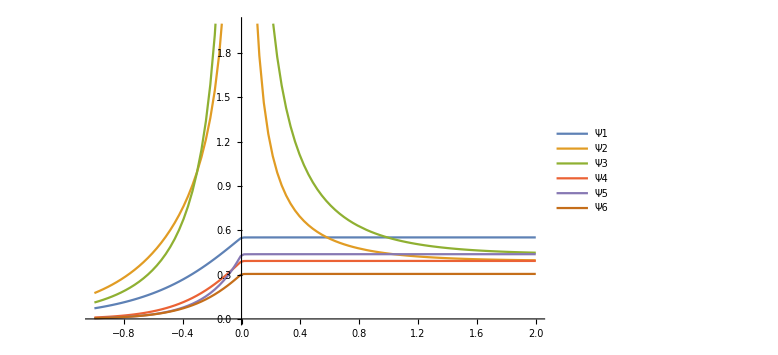
-Graphics-Log_10(P/N)

```mathematica
plot=genPlot["pts"->{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg},"plotRange"->{{-1,2},{0,2}},"xaxisLabel"->"Log_10(P/N)","leg"->{"Ψ1","Ψ2","Ψ3","Ψ4","Ψ5","Ψ6"}];
plot
```

## Figure 3

Figure 3 shows the evolution the bias and the variances as a function of the overparametrization ratio P/N
The function used is plotBiasVarRatioEvol . This function offers the possibility to pass the points as arguments and not compute them again. This is the method used here.
To generate the points again, remove the option pattern “pts”

### Generate points

#### Figure 3 top: low regularisation

```mathematica
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->1,"λ"->10^-5,"ψ1"->0.0];
(*in order to obtain more points around the interpolation threshold P/N∈[10^-0.2,10^0.2] *)
{Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->50, "minVal"-> -0.2, "maxVal"->0.2,"λ"->10^-5,"ψ1"->0.0];
pts1={Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg};
pts2={Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin};
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Table[Sort[Join[pts1[[i]],pts2[[i]]]],{i,1,6}];
```

#### Data λ=10^-5 N/D=1.0

```mathematica
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Uncompress["1:eJyN3HlYTfkfwPEzNFRKjSmMpa6thdBYky2E0LQYmcYyomWahFxJFK6EUCQZaZlCRpqYJMqSe7UoCmWXVFoUQiQT05jfOff4fc/H/Zxvz9w/5nnmeT/3nnPP/Z7ldb5HfZasmO3RgWGYVWrsf2x/WeXrsfqz/2sH/0/KKF+NcuneHcH5ye5pE1W6umFg46WOr+TS4K6TEi3STql2nQktlZt1Xsqlq88eexylf1q1d1/oWzK12wu5dNS1Tpes9pxR7cqPN2yQS+uPV+/NNMpU7cYx3mlXjJ7LpTm7mwtj7p1V7UPP1R/aOeSZXGqw+f3NqCPnVfuoB257vxv1VC6Vzc6K8YnIUu3K1Z9QL5fur6962BwvV+3TunFfoE4u/crymxdf1itUu51yAU/Y9XOtWTC7S7Zqd1K+auXSuE3f7K2wz1Htys2zsEYudZlXFX/yYK5qd2fX/oFbtVzaS0Pf8Yb6ZdXObZ0Y7yq59EzPrJSJW/NVu/LjfR/Lpfui1a526HlFtSs3f2ClXBoamtDQp+Cqau+o/IEq5NK6I+a5QbuKVHtX5Rd4JJd6VH88obHiumo3Uv5+D+XS1l1eKyaOLBb/fR7IpbOfqUvyrEpU+1Tl9r8nlxa5t7R3mndTfPvekUsvVM1u+Drolmp3VW6/W3Kpn6Hh+A6Zt8W3T4lcmnhUU6LReke1qym//w25tFF968DC7+6p9v7K71col+qtDziWm3JftVsr1z9fLg23Udwf2r1Utbso1y9HLj141Nb2i90Pxfc/uVzqtnvYmkqdR6o9+gD3OiuXFnital7ct1y12yiXnyGXev66bpbBAdTXL9/+vbzujFzqMMXI+/kfqP80Za127ch0udS81HHoiFEVqt2q+y/5msEn5VJvj7E1kkuoM8r1/1MuPfS8/XQ7vUq0fqUn2y1OPC6XltqeabQxQl0reI9filWSXFrja1ky1Bv14sErn/1VdojtN7bHm6ShXmnALT9eLtVNb54U+Qj1gX8evLD1TTT7+425ve7jX6ins2vXe1C4XJp0aWhuz/GPVXuL8ybzm7tWs5+/VdvLdAPqn94/UcocubO04nfUTfjls/3Muz9/SEJdotx+8WzXjDuaiPs1/vuzPcQ77V/cNfjtx3bvP2x+Oob6p+3P9pT8m9G488v/k+3pyzSO4v7p9+eWH1aai/un8cN2iy6Z1bgH8uOP7W9bnf4WWT9+/LK9SL3vR9w/jX+2ewb8rZ2M+qf9h+2NHummuHvy+x/XZxZOwd2W33/Z7rNH4oS7Gb//sz3hxqrFuGvxxw/u85ce8cLdjz/+sD1VpliJuwd//GK7rqf7Gtzn8sc/tjMWHwJw57ffPbYXf5mzEXdL/vjLfb+/XgbhPpA/frNdkRW/BXf+/P6I7TKdl9tw1+TPH9z6rWnYjvt6/vzDfX6/YztxX8Ofv7jtZzA0DPfl/PmP7ZWG23bh/un8yW1fSeZu3Bfx51+2OxTkh9O2by3bJWfO7cHdgT//s908KzIC9+n89QPXtX/ci/un6w/u8+doRuJuwV+/cNvnbrJIN+Wvj7jv3+7SPtwl/PUVNz6zx/yKew/++oz7fZgkkf4Vf33HdqsbWvtp+9cr7vP7/iLSv2C4VyPbXa5niXT++oPrirBOUbh/4DZPC9clHb8X6auV4+M1t/xrkSL9jfLjuc64l4h0fvy84dZvssYB3J+yV5fn6t8ov/84kc7vn01c9/IW6VXc6ldyPcEzSqT/pBx/b7nld7sk0kuVuyfXK88/Een8+GzmPn+fRjTuN5WHF2V/ZCrS+evXd9z2KZgu0guVF3BclwW7inT++vgv7vtPWC/Sc5UXkFyX9N4n0icqx38L16f+IdKVl/fnuK64Jxfp/P7xntt+TTdF+inu503jOpNeI9LNlQv4wK3/8GaRnpLMvbheGaIWg7uJcv/7m9s+V7uI9ERu+BziukJLItL5/bOV64vNRHqs8gKf6y6lo0U6f/z9h1u/rZNF+j5ueO7lOuNnK9J1lfv3R258pDuJ9FBu9XdynXH4SaRrKPf/f7n+vYdID1YCkeuKgmUineFfVuzvf95X2f+TVuefn9Zf0wNpiGjVbIdxu8caBVSt7moyCux9DWmIaFX98IKw8WmFVK0O++GX6A/nr1G1WmitN9jxxQ2qVof9OdAgrz/SDtFql23LRvfzQtohWp2w+HhzXgHSDtFqt9bqi88nI80QrWr2OK77zcO7VK2mdPUYbhSJNEO0anbz8GOHlUgzRKuRcR/nfu9XRtXqwRFupUFHkTaIVgPGBbq3BqOrcaLVW0einWpL0GgiWo19cP3doAnVVK12mJL3bv71GqpWzarVrcxCnlC1miqJeNAkradq1WuDR+i8qGdUrV5+rX5k6ZcvqFpN3z3nun3RK6pW7ZbHGUZtfk3VqvVmn5OHlzdRtfpy2InCAZebqVq12LSu06GsFqpWPX+u1397spWq1VQjo5krhnxhRdPq/ZlSNZ2uaqqdaDVhbMEYz4wvVTvRqou8MDiO6aDaBa3OXKrn56Gu2olWXdQj1TI2dlLtRKsKP49KtTWd0fr9X6uybWE9/FN0VDvRKnNWfXPpjS6qnWhVpqFpVPRzN9VOtMqUnCi5kddTtROtMv62ktXehqqdaJVJXzT4gaOJaidaZWTZ72YUWlDezx3No65kOxqrdkGrTPG3tgG9VbugVYbZNab0G9UuaJVhfLtv0VftglYZxdrOf+tStr+yh31roCW+fE6rjGzohVealN9f2Y9u1kLjQ9Aqw6ww74zGn6BVhvExzWlHGb/K/lP0etQFrTLM7dlNjGoXtMperqwIQvuXoFWGkcQt/4uuVfZy7mjnt3StcuufhI4fglbZAeBzHh1/BK0yTGzmuwa6VhlGXZ6Djn9Aq8yFnA/o+ClolT3LT95UR9cqe8lQYY2Oz4JW2ddai1q6Vhkmc8VsdPwHWmXebt+Jzh+CVtn1syqvomuVYWqmT0Nd0CrDeI5RtKFVdoAunNGGVhkmWFaBzo+CVhmm+x0Z6oJWGab10SDUBa2yr3MX0d08Qavs9t81AnVBqwyj65uBzu+CVhkmNbEc3c0UtMowldtkqEOtFscMRF3QKrt/aJSh6w9Bq+z4/zoSdUGr7O+jPxt1Qavs9w/UR13QKrv8/Efobq6gVYa5H5SMOtAqYzEjAHVBqwzjctEedUGr7P4bboy6oFV2+69uh7qgVfYAO6gSXd8JWmW3n58CdUGr7Pg1PIy6oFX2923ehrqgVYZJKlqOOtAqExXwA+qCVtn1ezQJdUGrDGNTPBh1QasM4zyyJ+qCVtnlN2qgLmiV3b517x/QtcruH+2fow60ytSbPUJd0Cq7fo7FqAtaZZiEhbmoC1plP9/qLOqCVtnf7/kJ1AWtsu+3O4K6oFV2/1wYi7qgVXb/0IpEHWiVUbcLRV3QKsNYf7MFdaBVxsJtA+pAq4zvAH/UBa2yx/85UtQZ/mWl/P7PvB/8R612X6TzMHPlBapWHwbPH2Ykv0jV6qqraQ9fJqC5R6LVpu8tl9769xJVq521g3bu2IjmHolWLw/ONr7bL4+q1cEmZT4dXiNtE63uaLyop9+AtE20mqC/ufVyD6RpotWay3v9725GmiZa9YwpHRnZDc0dEq0+rZn0oeNepGmi1ZfXdU/fHIO0TLR6ujEpI6YL0jLRqna/vx+uGIDm/ohWzSuqU/sHotFCtJo6xSyxvC86WxCtVvruW3PFBJ1NiVa37Bo9NswBXQ0QrUY8X3jYaja6WiFaXXpm0bKDx9DVENFqQj//u+be6GqMaNUjrnX8xIznVK1qfZWde/MUXase4b189tq9oWo1Y+rtcjUPpFGiVe8TWvbv3d9TtVo5bJRnePZHqlZ3fHFrwDSj9pSrbVaDq/PCbG4iDRCtJkyYe3fOfazB/2vVwfSu5fn+X1G1mtlsX7xaijrRqueI9qMC2+nRtbr9YUD7+UiLRKuVNgHGrvt60LXqGOGysw5pkmhV99nAvYMt+lC1WhkTMtnU1oiqVUXjvcEhAwZRtSobbjr1ysihdK2OWpRZMXoMXas+0ZqyGzPb0Kq0adoO9H6g1fs9h35EywdatVmzswmtP9Cqf8IrQ6RhoFXJ0zLdvm1p9f4/cRQtK7UquZ5l26sNrbowXnpI01CrUxRZSNNAqxKXD0O+bkurpq6P0d0KoFWrheGmaPwCrcru/GCPNA60Kuv49RF0twZq1bfjY6RloFVZL7vhSMtQq6HuPyMtQ6329XNAxw+oVca07F1bWm3sV440DbVaX2yB7rZBrSpO3kPahloN7pPS2JZWnXPmouMr1Gr/vGh0NxFqNeVNN6R1qNX6tFykdahVk5UHnral1e69wtH5A2o14cphpHmo1bJVxUjzUKu++V1Qh1ot+vgzOr9Brc7Ju4a0D7Wq1Xcy6lCrsX0c0PkVanWcfh3SPtTquMHbUIdatVk7FHWoVca4oo25VXb7rt/Xxtwqq60Hjm3MrbLj74+v25hbZceXtBTdLYBalZ0/gjrUqnOf1ahDrfa3sUEdalX2yAD1z7Q65DW6foJatXBPRh1qNbPWE3Wo1e6TzVCHWq3v+hbd7YBaddBQoA616n95N+pQq+btXVH/TKvrxqAOtcq86II61Kqkzyt0NwVqVfH4GupQqyYfT6AOtZo6IwJ1qFWTmDWoQ636FP2EOtSq4tx0yt0kXqNJU4ehDrXqbG+AOtRq0oVOqEOttqz6gK7voVYTFj5DHWrVxu0h6lCrzquuoQ616uCvQJ3hX0qtqi9JL/uPWr0T/2bwiAubqVpNP5zUfv/mrVStmo0/a7znj+1UrT7Z7nhqtVUYVasxHXQffzwaTtWq+8DSPafeRlC1WnV72h9Xdu2javXUkqGd926MompVd0GvxY4lMVSthi2zDJyyO56q1ctvO6+6X3WQqtWfM+MmvrdKpGp13UWbxLFPf6dqVSta65/F1ceoWu0anvvq9OjjVK1qOp2YJVuTStVq6A3JyQnb0ZPgRKv2tcljq++kU7X6e/7g5AVLMqhadb2bZnhs+DmqVm/tnBJ60Q49qU20euHszpBRC9DdEKLVLXOGuMRZoiexiVZdR+T0jbVGT1oTrbr8edK4LgDd7SBavffFRLXsx+huB9FqZFhtdoUfuttBtOpoNa/Kaix6UppodfQwta/U96O7HUSrQwyaZ8mN0LMBRKuW8SOv6cxCdzuIVjc0PEn+rhB1YW7V5OXk0xWoE61K6kPOHPBDT1ITrda0ux/xmw66m0K0GlW7zy44CHWiVZus7Y7xyagTrZrP8LRbNh09u0C0yqxcF51bizrRaoL/K+lpG3Q3h2jV6kqusfEW1IlWZfcWBQzvj56NELS6YFJjl/OoA60Gxur0wPdmBa1aHdjYG997FbTq89twA9SBVm0i1A3xvU9Bq403a3EHWjWXrpJQlq/UqlW7cNyBVisVd3AHWpW19u6D75YJWpV964Q70KrVpfm4w7nVYhnucG41+RLucG414yPuQKuyKcZ9UYdzq72tcYdajfkRd6jVkV64Q62OWoM71GrnINyhVj/uwB1q9fcI3KFWpVG4Q63O+w13qNWqQ7hDrfY/ijvUakgy7lCrbsdxh1odkYo71KrkFG378lpVP4071KpJBu5Qq/WZuEOtFp3DHWo14Tzun82tXsQdajVUjjvUqr8Cd6jVhku4Q60mZeMOtVqWgzvUqk0u7lCr40Q61OptkQ616ptHGz+8Rt9exh1qNVikf6bVfNyhVm+LdKjVcQW4fza3KtKhVr1FOtSqj0iHWu11BXeoVTWRDrWqexV3qFVfkfdDrfYSeT/UqoVIh1qtF/l8qFWxz4daZQpxh1rVE+lQq+oiHWq1TGT5UKu5Ih1q1Ufk86FWw0U61KqZSIdaLRDpUKuJIh1qNVKkQ61qFeHO8C+lViXK/p+0etY5om7JlNVUreYqpub94+pP1+rCdNcl7wOoWs3660frkZoyqlZXWvbuNMgtiKrVxOyeh8P1t1C1ukjvjW/TwBCqVhNSFg5JSttJ1aqiri5UM2s3Vav+BV6arkOQlolWbc01AyNvRVK1utZvvv2k0v1Urbp0u31uugPSMtFqqW+PxrVTkZaJVhPuDP3mTS3SMtHqRb/t8zoHIi0TreZUbZt6w+coVatFQYc2R5UkU7X6oix044njJ6ha7e5k+cO4nSepWp03LlXviQ7SMNGqdnx5qGEj+nfPRKunMsbFZFsgDROtHlnfI8yrBWmYaHV6TqnLHUM090+06pJmYZAYjub+iVYj7F+YWv6ItEu0mqlXlxK0BT0pT7Sa6er04FZfNHdPtFoQOPWLf+ORZolWi8dm3X5niTRLtKpYOSMn4R3qRKuNFRvkz/ToWjUxOBWf1II60Wrq0RijXU+QZolWE5waZE1xdK3qqh3b8bacrlWHhoxJJlV0rVYeGv/P7EakTeFJ4CSXFdFxSJPC3OqwOa7DNdDRVNBqn+UjSwaiJ5UErd5vUN81DT0JBrTqPKn8H9SBVi/MjFBD9x6BVp03vf4SdaBVn457OuJ7n4JWXW5ZaaAO51bHO2lSlq/UamW7MNyBVq3M9DuhDrXa9xDuUKut2lp4/QStyvJ64A60qhjoijvUasFj3OHc6htnbdTh3Gq/JNyhVr0qcYdaDdDsjDrU6pOBuEOtplnjDrUa+yPuUKsNXrhDrXqvxR1qNXEL7lCrE8Jxh1qdfQB3qFXrg7hDrVol4f7Zk8AncIdaLTqFO9RqSiZt+/Ja1crCHWpV7xLuUKu+ubhDrQbm4w616nYVd6jVBTdwh1q9UII71GrILdyhVhfcwR1qteYu7lCrofdxh1oteIA71Kr5Q9yhVk3KcIda9X9EGz+8Rh3KcYdaHVFB2z95jZpU4g61qvYYd6jVIpEOtWpdRRufvEYbRTrUang17p9ptQZ3qNUUkf6ZVmtxh1pNFelQqwUiHWrV+Qlt/+A1minSoVZbRDrUqkUd7lCrziIdatVfpEOtMvW0/ZPXqLlIh1p1EelQqyEiHWo1SaRDreo+xR1qlRHpUKti74dalYl0hn8pteqi7P9Jq1EfDK2nGdO1qp1teqrjRLpW3VKXrLleQNdqRsCes1G3N1K1+q/nwswplnStzno60Di8PJiqVe3I8rtXq7ZRtTp2h8tEzTl0rfqcOfi20yS6VhM26W41f7SHqtX9ZR9m2f1C16r7jIVnJ9nTtfret6fBb9HRVK2mfXulZYLzb1Steo7VvzhkFl2r2jt6r3BMO0zVat+0MwU9vNDcLtHqzdSWTRUBaG6XaPVWpd2qU69TqFr9UdFFz3wpmtslWl1QvrvrsWg0t0u0emaG4fTx2uiveBGt2jT0vqN7Bc3tEq2O17AzmXMbaZZo9UNAxNc9RqIn3YlWE0bWDdrTguZ2iVbzr+rkFXZAmiVaLZBMVXeZjp5kJ1pd7jTfuuQ8+itZRKvZTw9mXndDfwWLaLWmLCwu1gX9FSyiVR/bOWuaJyENE62+jYzXbnZHnWi1u3u/BpeVaG6YaLX+tb59VhD6d+VEq7lzLb4/Y4K0TbRqIjNf/8IWdaJVhUeoydiHqBOtKtY7d/zKGz1pT7Ra6VDXfUA+6kSrihkhl5l/UReeBN5/zS03Amlf0Oq0ztc/GCLNA63OHfzzWtSBVs22HwlEHWg12Nt+PepAq/fdum9AHWp1xFPcgVYTypZvpCxfqVWHW9txh1pNKsQdaFVyXUeGOtRq0xTcgVYTJDNxh3OrhstwB1pVzE3GHc6tNlXjDrU6WnMT6vBJ4JUDcIdaPT8Gd6jVZTNwh1qtdsIdavVLF9yhVhd74g61umQF7lCrdqtxh1r1XIc71GrxBtyhVhODcIda1dyKO9RqYwjuUKtRO3GHWm0Io21fXqudw3GHWn23B3eo1cS9uEOt9t+HO9Rq5K+4Q602ROEOtcpE4w61WinSoVaLYnCHWo2KxR1qdU4c7lCrzG+4Q63GinSoVbN43KFWE0U61KokAXeo1ViRDrXaKtKhVj0P4g61qhDpUKuSQ7TxyWvURaRDraaIdKjVFpEOtTriMO5Qq54iHWo1VqR/plWRDrXaKNKhViWJuEOtWot0qFUfkQ61Gi7SoVZTRTrUapFIh1otFulQq2pHaMdfXqNaIv2zuVWRDrU6QqRDrS4Q6VCrPiIdalWsM/xLqdVArv8P05y4SA=="];
```

```mathematica
{varIn,varData,varNoise,bias,tot,plotlowreg}=plotBiasVarRatioEvol["legPos"->{.825,.8},"ψ2"->1.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-5,"ψ1"->0.0,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 1.0,"k"->1,"pts"->{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}];
```

#### Figure 3 bottom : high regularisation

```mathematica
{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->1,"λ"->10^-1,"ψ1"->0.0];
```

#### Data λ=10^-1 N/D=1.0

```mathematica
{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}=Uncompress["1:eJyN3HlUTW37wPHQIKWJBiEhKZoeQwNqV0RSppRIg2TIm2SX0mioaJJKo4o0kyhCKh0kzUmlRCkNQoZKplDvcc7zXu/vd673Xus5f1jL+i45Z5+9731/znWYbXdw8x5eLi4uF27mL8YOLq577P/f78b/39/RXKzHAINeryf+kr82j+LoE2d5D9zn+8Sgh982ODWOu8HZhXW+d/oJf2TQIZ9sTHPW5nN2KSvXJwaSHxj0GdN9i+n0m5yd9eNnvWfQbs/l8r+K3+bs8xMcr1fK9zPokqy0EJ7EAs6uWvgmJUTlHYOe9HFc9XbNQs6u3mp/1kT9LYNuTtyy+nx/EWdnPX2dNwx6s7/feKtbdzn7ask/L6CPQZe97o0aF8/g7OtZf8FrBh0tPCW/t/IeZzdjPXoZdC//Che7xvucnXV4rHoYtKyI1fq2Nw84+27ms2+172bQcY/USsUmPeTsf45OgmMXg3725JBjvHoZZ2f9eNdXDLq2s7n/yYFHnJ11+L07GbRDQeTy11fLOTsf6w3qYNDaUyU/lH6v4OwSrBfQzqCzHdb8ljKq4uzyrPfvBfP8UOwcZ3qx+n+/P60M+qsUw/firxrObsA6/i0Muqv15axf2+r+9/F9yqDlNfy2K99+zNl3sY5fI4N+cly7fCCw/n8fnycM+nxbgXj74iecnZv1+h8zaJPO0md/vUBdjvX6qhn0Lfmwnc0+DZx9Fev5lzOPj/Qgf510I2e3ZT2/UgbtKnTJUy8Pdfb1x2DQ/K6qmwJ0mzi7Ievn32Zev82Po2dWoM7F+vPXmO9f8Ix3d9c85eydMn/6BQad6zlcuZqBOnt9SF5BFylmh95Taebssqyff4GixeLifm6JIfRrFG2s7bbR8Cvqfz9/ilY88Grd0PoWwuun6KvRoV23k1Hfxz5+FO3aP1TN8x51Y/bxp+gVGyaLGv/1jLMrsd8/irYoa4obcUZdkP3+U3SF/ZUE32zU3djnD0Uryau36b5CfQ/7/KNoq+8vj6WJtXJ2c/b5S9H+he/38+qizj4+LRSdlNjbX+yA+jL29UPRDXI6DMlw1Bewrz+KVpGwX2x7A3X2+txO0by7Bg+1NqI+iX39U3SydMvze4Oo+7DXD4o+ph7rsH7yc87uzl5/KPrGTC2Zm/KoO7HXL4rep3lh91wd1P9e/yjaXMDGt9QUdRv2+knRhvymz4r2os4+vr0Uvcel54CqJ+ob2es3RbdTsRI6IaivYa//FP3N5H4DdwLqf98/KFpINFrk/CXUNdn3H4qOs3n8bvZt1P++f1H0gskHd2aUoq7Ivv9R9GTHN6HUY9Rl2fdPiqbdjWrGWlGXZt9/Kfrcq8qP37pRF2Xfvymay332No0PqP99/6dojTNq82u+oD6OtT4MUHTJKU2j0t+os+8vzD46XyxNgecFZx/5c/i+M/v0W9mz+ARRP8w6fwYpuqdAqnyfGOpDrB/P7H6TDreYS6HOPr+GKFpYuLmhdSbqb5lHv/ANs5un+4b/mIM6+/r9TNHBRf7r7s5HvevP0+9k9lAzsdyFSqhbs87PYYoeWba3z0gN9eesy5fZ5zoUp8guQZ19/n6h6Kpi+XnXNVBvYC0/zH6R76wx93LU2fuTrxQt1TUUP10H9WrWDZrZU35e1fylizp7//ONosP2HOK5vBL1h6wNArNLWlpEKaxGnWJdH98pWlo+Wd3LEHXW6V/I7HN3PxlLM0Kdff38oOhs46NVWcao3/jz9l5n9vMeySuC1qOuxvoLRig661ZIteFG1K9c/vNg9pp5FxlvN6GuwLr+flK0gl2mhpMp6ml/Tp8UZndy6F74bAvq7OvzF0XbHhx0VjRHPZG1gWP22bPtC3dtRZ29Pv+m6BdmqkmBFqhH/zk9zzI7X05XRPw21EVY1/coRa9UKfgaux310D9PP4TZlyd4igZYos7Puv7HKDqqZrWo3Q7U/VkAYHbfuQtF1KxQ52I/dOm9jZlTB/70f6SR6QUHgjra0W4XNGK3rq6wQQ/tZkEjKnqfrK0K0W4WNGIxrVFnimElUSNVfldk9vWj3SxohCv/SFp6Gtqtgka2KNJUhwvarYJGvpuve3NICe1GQSM1aeecYhTRbhM0slleL6pXDe02QSMaiwUts/TQbhI08qhvxrK27Wi3CBrJsOMVl/dCu0HQyIq1Dq8fJqPdHGhEKXWhQEAl2o2BRvYLfj9zcwjtlkAjaYOl+2dPQ3cT0EhMXae4sBY620Aj46Wc6bXr24gaOX/F5ueSLe1EjYw3ynr92eAlUSOzlkecPSfTQdSImZXCHpdW1EEjSUvjJ8zX6iRq5KWqwdK3NOqgkd57cW6v41AHjfxYFn3/xmXUQSNRIWIZKVmog0aMZXfOvHsWddBItpmny7UDqINGRCdU5qRqog4ayUigLyt8RMcHNHIsxHRo2VbU2esDUyMTrwZPS8tD7w9oZJHQofuLxxM6UyORdxdYLjFB7z9oxHHo7fxNMej8AY0kFnJJhXWi8w80MtSjLG2igjpopErvt/aO4+j8Bo2E7951ceILtNsGjcS0NQgvXoE6aETIePIi+3SyRmR583g6JFAHjTQ3Z3zPDUfXL2iks/qRG0MMddBI/eGdYw2JaH0AjTRl+49dwJoEjXBr9ZXUlqP1BzQSaHMm9+de1EEj52x9XMqEUAeNzCn49KisCK1/oJHXH8qy45xQB410HT3b1SaPOmikK7j7/ZIetP6CRo7e2Zy7JgN10Mgx9fDGe46og0ZOpg73bdRAHTTCHS3glMODOmhENHeMEd6C7h+gkRmTFr67cwV10MiR8O/u7/1RB41sbcrSGrBBHTSSmL2ZN0IbddCI7bEg7/MzUQeNrP9hXdo/hu6PoJHN9EfjDT2og0ZseVckpFShDhoxOf6a78F11EEjytO/hIUmog4aMTzZldh9CnXQiFTzu47LrqiDRroMwmZU2KEOGpl1U5ln7mbUQSNHVZOmpuujDhpxKvb7l9YS1EEjKRJWuTXyqING+KYODhpLow4aqeqfGnpJCHXQSE55iFDjBNRBI9rP2ucV/UD7I9BI19qxgC0DqINGsitTmiP7UAeN3MgVv7i/A3XQyNCmk9STFtRBI5e1Y2uL61EHjbwLkZOWq0IdNDKyc8650VLUQSPSfT47VpWgDhpRKeof/VCAOmikoCQ8dfgG6qCRtGiXvk3XUAeNzKnIaB27jDpo5NL9GZ+/Z6AOGrFWlBLWTEUdNKKmrmRfcAF10IhE1n2fw4mog0bcuSXU/xWPOmhEJDI7NzoGdS72Q5e23DbbbPBs/T/UyJTfWTE2e9FsATRyJMixx3ZbMVEjK0xr1sYfLCFqxEPOa1DFHM0OQCNmdxfO5wtCswPQyNGEVYcCnqDZAWhE7P2J5EY1pCnQyC7FmwsEs9DsADSy/VvVFhVNpCnQiOXk2HdCXWg2ABrhnrDy5aoMpCnQSNGpXaqiAUhToBFFobZ4PV+kKdCI1Nt1/ScN0bsNGrHw39HxzQqtNqCRVGOlu8t90d0GNGKWP13kTCa6m4JGVvft33e6Be0GQCMXHLjnywqg3Q5opMP6RuBhHbSbAo1k5bTf4D6AdmugkVA+u0upEWg3CBrR757w83oG2m2CRkTFhXNtM9BuFTSyYG1s6Vgw2g2DRrr49G47bkC7adDIiOdzIZdPqING9o9/WC+3D+3WQSOWPgvKxAtQB43o/PU1xLkDddBIw6vWe124g0am8R5U2F2MOmhEeBv/0Lsj+M+zHkyNOLt9fcsjTdZIPX9SdWgaev2gEcFeuyyTmWSNxFybwdsQSNbI/q9D+ur9ZI1wN1c/FMOfvYFGHuTy33VJIWvkquaXKy9+kTUixNc43mQbWSOhbRPubb1D1oiKumezggxZI7m/dqTEB5I1Eml93EfnB7q+QCPm2jkvXZzJGunhsalw+Ii0ABqp41U+puxC1sickdTMvFF0/YNGRo4v72wKRx008iDswoK9imSNDHVyLVKpQOsPaMR4kkDeG6wF0Mjr6+umbZIka+TklN3Js8rR+gcaaXs8Wi/gjTpoRLZqX0HtUtRBI2kZh8tkhtH6CxrZ26rvUHgLddCI7IkDp6x9UAeNDB8PvFe9BnXQyKpX7hfKxFEHjUj1nc4Vw7tF0EilTvMp7yLUQSNbvzUWPo5EHTSyqHvSkxeOqING3ucOKLusRR000n/L+Ot+BdRBI6rKsUPn+FEHjfS4S3QUtqLZOGhEMCR7uUwa6qARN4053TNp1EEjsstnc3uvRB004tx7u2lUEnXQiOD6FWbOn9D9HTQSanJQ/Hwl6qCROe5zf1lkoA4aebk8RPRwAOqgEUFTyrhyD+qgkVBlrp2qRqiDRioSFkT7qaIOGqngrz+bJoE6aMRb08rAZayWqJGCyFuXGt6iDhqRq7uan/kUddCImGyRUusD1EEjFpfKQzbkoQ4a2Zwn1DWcjDpopCbjaWF+BOqgkasRn8d7+6EOGhk+xTOo6YY6aOR6lfqn5w6og0Y6Lf1ObrZGHTQiKGK1LsIUddCIzq7E6qC1qING9kdk+qjqog4aOZZTlOumgTpoRCJtle8WVdS52A9dOmbZouKS+bX/UCN9Uuefb/M/QdRIZqTO8ibuAKJGzj5vDB98eoqokaTQoEFvrhCiRuof3K7oOR1G1EjYzNtNUqsiiBpxl93H/9P7LFEjnRUphdLfookaWRtaayxbEEfUyJRr1K0HZQlEjYxcuSqRNe8CUSMR3j/5LzhdJGpE4ZJpysMjqUSNiMmduHT4RjpRI8/tykWcZbOIGqmbIx3Reu8yUSNTnGdkSEbnEDWiNXnOftP1uUSNTNCOFxx5h77pBxqRSe2eJ3MBfdMPNNI8Zc+3wn3om3ygkchfgvPnGaBv8oFGkvZ0qIn+dYeoEc3ZDzanK6Bv6oFG1mulW8fOR9/UA42oFZ9ZY6aIvqkHGtHc7VpyLgppGzRiOVN4s1kE0jZoxEz5Rn5hINI2aMRTd1Fy35FSokZm1CXwGNgijYNG+DV2aUVoI42DRp64+O7uEkazT/b6wNRImFHK1NRm1EEj2lk8esERSPOgEa2Vp0LCdZHmQSPG+pYLerpRB43I83s0tXmh2SpoJNRG5czARPRpwH81MnKw91II6qARO8P3Dy5wo28SgkbGWb0adnJFHTRS33lU9eYL1EEjk1PM7CcvR59GgEYSlvKoTT6LOmikykFw/soe1EEjV6eIP16K7wagEfPsZ9N2uRLudkyNyBp46Ojmow4acX3u+1TrE+qgkfaWsdn589BuBDSyTvK+u4AF6qARxpjZ9aiTpE9jKHqba0J+Uh7qoBHbbNd3B1oJuzmmRjz4kipWj6IOGpkg/niNvSzaTYJGgu1Dtv2mUAeN0EeDzFZZoQ4aWahqb7P3COqgkTybgw/DI1AHjTRL9mzqy0IdNDK9+1ZqWAnqoBGJDn/HzAbUQSNDSiK3N/SiDhp5ZlA5O/Ur6qCRGsFDwVYTyBqJHMzzaJlE1oivevvcKlGyRuYIi7hRUmSNCEzLjNWVQR008kbt9cjTuaiDRuQuT3PkU0QdNGJcbj6rTRl10Ihd4e/i7YtQB41Ey804EKSOOmik5Ff1qwPLUAeNSI9k2k7WQR00YirpWO2ohzpoZK5Hc2b4KtRBI/sGnsv7rCHPRha4ay1UNyLPRrwtT25gGJNnIxM25vVP30CejTjpSUpv2ESejQxfUCy2NCXPRnqK8n1XmZFnI5/ba9sFtpJnIwPvnBXyLcizkdELTX7UdvJsROmh18drluTZyAYx/pV8VuTZSJrwi2VrrMmzkS+Brs6HbMizkZm/b+48ZUuejWxv7T8UvJM8GykWutnvZUeejZRolo232kWejUTpBTxVsSfPRu6pRTsN2f/T2cj+GYKh5167EDVyqr2u0zbfjaiRcyqv0ud2exA10vb0qfo3Xx+iRvRyZxbHVB0jasQ9Wa/rL2k/okY6s2uvGdxCWgKNVJcp8h/ODCRqxGhI+TffN6Ql0EjfnE9eHVfPEDXCL/m2/dp7pCXQyNBnG6dM3SiiRnz0c8IansUQNSJ39M5gemE8USMvN1On7PsTiRrpSFVS+qKRTNSImqahnLp8ClEjkXtDiyT004gaKe9YR8WEZhA1ciBm2e7XPJeIGrHgCdLTy8kmaqTZw//9w2NXiRr58dlXIKcEaQk0Ejk684TZhutEjVwPqKmJ/YS0BBqZxGuUpJCItAQaWVtlLGC6CWkJNHJoaePQLAGkJdAIr4e4mV8ZYTb5ZzaiX9wf7I1mk6ARIU/+T4FKaDYJGnls6PxCvQFpCjRi42letucm0hR7fWBq5MeQXfdET6Qp0Ejvbz+xhepIU6CRST4fRZa9RR00ohVt5dcRibQFGpnpNRr1YxHSFmhkzrzRjohK1EEjZ0Xy3JrMkcZAI0us85P4XqAOGqn7aRHob440BhqJ+/xYI68SddBI/aI7Xj+XIK2BRnQdhn83xaEOGgkzeKWZ+wV10EiFdvDi0XVIc6CRqaUfOpQSUQeN3PKpGkl/jTpoxL81dWPdQqRB0EiGpNFGHkfUQSNZ9adb0jJRB40Mh1xeMK4DddBITcvqSQ5iSJOgEV3/Sy/n6aMOGhGcMjbg5YQ6aMR4y6acy7Gog0akpmi+fX8XddBIgY21kscr1EEj22Vrvh8fj7QKGrGN8BdVn406aERqq1/JPW3UQSP3bnpNNrJAHTTSeX5M6Jsz6qCRiao9wu9OoQ4aKbB8UaefhDpoZOqOzVdl8lAHjWzcn98VV4o6aORZy/KkqibUQSP1544vru5BHTTyLGV0Ze5n1EEjnfo3Wk6PQ5oHjRQcUTjuJoQ6aERhy+8jXtKog0akzqgVXJmHOmikp8JUZJoa6qCRZ4KNenVahE8rmNrIsj0i0qqPOmjkmNZGc4N1qINGnHtFxGVMUQeNPDOUO3lgO+qgkaZSZ0XtnaiDRmpu/GyI3os6aKSg0uf20QOog0Ysdo+5j3dB/b8aWRGhNO8I6qARtY7FTh+9UQeNhI8fs7E/jjpo5N7cuNuh+LsroBHHJN4yxyDUQSMzVIc8+E+jDhqxr93qvDccddDI1CjGQDD+NAo0cq/i9zf3GNRBI/t4AlcsikcdNBLetWfx3QTUQSNyZdVTZ5xHHTTysHFT56Zk1EEjzgEDtjtTUOdiP3TptuvpaiZ//qXFP9KI6ew6/++1ZI18Lw3dYR5F1sigjnW0/x2yRtboBpweMSRrRNxW9dbFTLJGwo4E8Y37gGY3oJGTq7IrvnqRNRJ0bs/XnTvIGjm0Pr4lNoaskTPbkjLXLyZrJFlziwgjiayRfdlt/dPa0OwGNBJvKZCntI2skY8f/Kil08ga4RrmEZosS9ZI7T5f4c/OaHYDGnHX7u6WP4VmN6ARzxnKZTe80ewGNFL8Y5nq1Hg0uwGNuLuvsnF4kUnUSN31IJFePTS7AY2ox3wpu1l5hagRdcY2J66D14gakfdujz8sgWY3oJGjGif6232RVkAjbz0qn/h/QFoBjcjFOQpy2SCtgEaGVM5RzY9vETUyai6pnbkC/S8NoBHeL80em1KQZkAjOnE2z0VGkWZAI3Rn85IoE6QZ0IhUsrPPxDNoNsReH5gaecwQnCV9H2kHNBLkPFX1YxfSDmhEYtr0vkmeSDugEYMoZ1FqBHXQiJN+WqAqjTQEGrHwvbpAvAt10Eg6l7aAjhHSEGiEcpYs581GHTRycnXsryZupCXQyHGHD11iFqiDRtr4i3oXpqMOGnnaUSIb/J4w+2JqRGZRSVSUCtIWaETtTcJAzr9QB40InbpSuzgNddDI1x1WK32foQ4aCb+0vahjItIaaCQ4U2A4bSnqoJGPNw3mitugDhpRv+KiQgegDho5YyI38B1/0xY0krZYIuBVJeqgkfuHjybavEEdNGJ9PLIihRtpEjRCBy2pbZZBHTTCKx/WP1cDddCIZmSK4jUT1EEjneM9os/ZoQ4aedid4cfjhmeT/9EIv4dmpWAg6qCRiU1TB6viUAeN7N8hdMAiC3XQiJJr+4PqW6iDRm6vW3tT6yHhf0lh9tiTZQ4361EHjQhLVwdvbEMdNPLkkdre6X2og0YErR4KzRtEHTSiK2Hn6DWCOmhkp2Sp1cIJSPugkeomjUpdAdRBI/fLffMeiaEOGuEu6V5TPg110MgRmfpf62QJn1YwtbHkyUCYlTzqoJH3QlOmcSuhDhqx12qWWfMX6qCRwnHr45TVCd9UZ2qj+njOr7vLUAeNNEeIGo/qoA4a0fPxlRrWRx00or92bljaatRBIwbjPntONUIdNCLTn2JmaII6aKRGcvqqVRtRB41cO7F7tqAp6qCRjxXyfqlmqINGgrwvl0y2wN8N+I9G0hVCP5hsRx000mXAM7RnB+HfXTO1sSG5z9PSGnXQiO+oEZ+KLeqgkSG94bedO1EHjVzM8jJ224U6aER5u8aiAXvUQSMq3z56btyDOhf7oUtLeu7ojdtbTv0bWXhW4A=="];
```

```mathematica
{varIn,varNoise,varData,bias,tot,plothighreg}=plotBiasVarRatioEvol["legPos"->{.825,.8},"plotRange"->{0,1.5},"ψ2"->1.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-1,"ψ1"->0.0,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 1.0,"k"->1,"pts"->{Ψ1highreg,Ψ2highreg,Ψ3highreg,Ψ4highreg,Ψ5highreg,Ψ6highreg}];
```

### Display plots

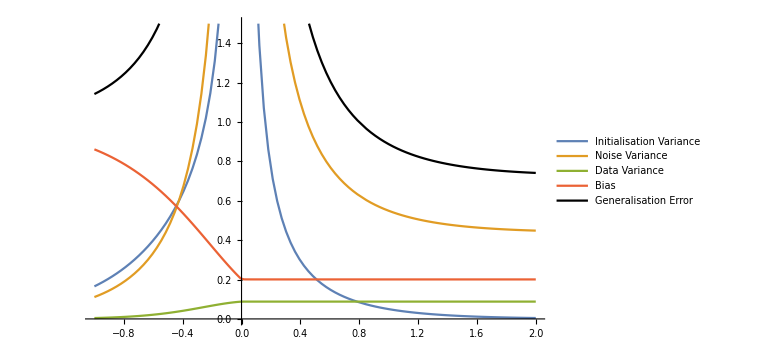
-Graphics-Log_10(P/N)

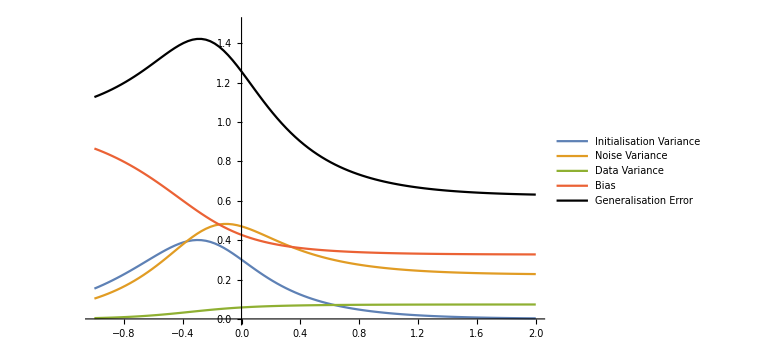
-Graphics-Log_10(P/N)

```mathematica
plotlowreg
plothighreg
```

## Figure 5

### Generate points

```mathematica
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->1,"λ"->10^-5,"ψ1"->0.0];
(*in order to obtain more points around the interpolation threshold P/N∈[10^-0.2,10^0.2] *)
{Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->50, "minVal"-> -0.2, "maxVal"->0.2,"λ"->10^-5,"ψ1"->0.0];
pts1={Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg};
pts2={Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin};
{Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6}=Table[Sort[Join[pts1[[i]],pts2[[i]]]],{i,1,6}];
```

### Data

Analytical data

```mathematica
(*lambda=10^-5 psi2=1.0*)
{Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6}=Uncompress["1:eJyN3HlYTfkfwPEzNFRKjSmMpa6thdBYky2E0LQYmcYyomWahFxJFK6EUCQZaZlCRpqYJMqSe7UoCmWXVFoUQiQT05jfOff4fc/H/Zxvz9w/5nnmeT/3nnPP/Z7ldb5HfZasmO3RgWGYVWrsf2x/WeXrsfqz/2sH/0/KKF+NcuneHcH5ye5pE1W6umFg46WOr+TS4K6TEi3STql2nQktlZt1Xsqlq88eexylf1q1d1/oWzK12wu5dNS1Tpes9pxR7cqPN2yQS+uPV+/NNMpU7cYx3mlXjJ7LpTm7mwtj7p1V7UPP1R/aOeSZXGqw+f3NqCPnVfuoB257vxv1VC6Vzc6K8YnIUu3K1Z9QL5fur6962BwvV+3TunFfoE4u/crymxdf1itUu51yAU/Y9XOtWTC7S7Zqd1K+auXSuE3f7K2wz1Htys2zsEYudZlXFX/yYK5qd2fX/oFbtVzaS0Pf8Yb6ZdXObZ0Y7yq59EzPrJSJW/NVu/LjfR/Lpfui1a526HlFtSs3f2ClXBoamtDQp+Cqau+o/IEq5NK6I+a5QbuKVHtX5Rd4JJd6VH88obHiumo3Uv5+D+XS1l1eKyaOLBb/fR7IpbOfqUvyrEpU+1Tl9r8nlxa5t7R3mndTfPvekUsvVM1u+Drolmp3VW6/W3Kpn6Hh+A6Zt8W3T4lcmnhUU6LReke1qym//w25tFF968DC7+6p9v7K71col+qtDziWm3JftVsr1z9fLg23Udwf2r1Utbso1y9HLj141Nb2i90Pxfc/uVzqtnvYmkqdR6o9+gD3OiuXFnital7ct1y12yiXnyGXev66bpbBAdTXL9/+vbzujFzqMMXI+/kfqP80Za127ch0udS81HHoiFEVqt2q+y/5msEn5VJvj7E1kkuoM8r1/1MuPfS8/XQ7vUq0fqUn2y1OPC6XltqeabQxQl0reI9filWSXFrja1ky1Bv14sErn/1VdojtN7bHm6ShXmnALT9eLtVNb54U+Qj1gX8evLD1TTT7+425ve7jX6ins2vXe1C4XJp0aWhuz/GPVXuL8ybzm7tWs5+/VdvLdAPqn94/UcocubO04nfUTfjls/3Muz9/SEJdotx+8WzXjDuaiPs1/vuzPcQ77V/cNfjtx3bvP2x+Oob6p+3P9pT8m9G488v/k+3pyzSO4v7p9+eWH1aai/un8cN2iy6Z1bgH8uOP7W9bnf4WWT9+/LK9SL3vR9w/jX+2ewb8rZ2M+qf9h+2NHummuHvy+x/XZxZOwd2W33/Z7rNH4oS7Gb//sz3hxqrFuGvxxw/u85ce8cLdjz/+sD1VpliJuwd//GK7rqf7Gtzn8sc/tjMWHwJw57ffPbYXf5mzEXdL/vjLfb+/XgbhPpA/frNdkRW/BXf+/P6I7TKdl9tw1+TPH9z6rWnYjvt6/vzDfX6/YztxX8Ofv7jtZzA0DPfl/PmP7ZWG23bh/un8yW1fSeZu3Bfx51+2OxTkh9O2by3bJWfO7cHdgT//s908KzIC9+n89QPXtX/ci/un6w/u8+doRuJuwV+/cNvnbrJIN+Wvj7jv3+7SPtwl/PUVNz6zx/yKew/++oz7fZgkkf4Vf33HdqsbWvtp+9cr7vP7/iLSv2C4VyPbXa5niXT++oPrirBOUbh/4DZPC9clHb8X6auV4+M1t/xrkSL9jfLjuc64l4h0fvy84dZvssYB3J+yV5fn6t8ov/84kc7vn01c9/IW6VXc6ldyPcEzSqT/pBx/b7nld7sk0kuVuyfXK88/Een8+GzmPn+fRjTuN5WHF2V/ZCrS+evXd9z2KZgu0guVF3BclwW7inT++vgv7vtPWC/Sc5UXkFyX9N4n0icqx38L16f+IdKVl/fnuK64Jxfp/P7xntt+TTdF+inu503jOpNeI9LNlQv4wK3/8GaRnpLMvbheGaIWg7uJcv/7m9s+V7uI9ERu+BziukJLItL5/bOV64vNRHqs8gKf6y6lo0U6f/z9h1u/rZNF+j5ueO7lOuNnK9J1lfv3R258pDuJ9FBu9XdynXH4SaRrKPf/f7n+vYdID1YCkeuKgmUineFfVuzvf95X2f+TVuefn9Zf0wNpiGjVbIdxu8caBVSt7moyCux9DWmIaFX98IKw8WmFVK0O++GX6A/nr1G1WmitN9jxxQ2qVof9OdAgrz/SDtFql23LRvfzQtohWp2w+HhzXgHSDtFqt9bqi88nI80QrWr2OK77zcO7VK2mdPUYbhSJNEO0anbz8GOHlUgzRKuRcR/nfu9XRtXqwRFupUFHkTaIVgPGBbq3BqOrcaLVW0einWpL0GgiWo19cP3doAnVVK12mJL3bv71GqpWzarVrcxCnlC1miqJeNAkradq1WuDR+i8qGdUrV5+rX5k6ZcvqFpN3z3nun3RK6pW7ZbHGUZtfk3VqvVmn5OHlzdRtfpy2InCAZebqVq12LSu06GsFqpWPX+u1397spWq1VQjo5krhnxhRdPq/ZlSNZ2uaqqdaDVhbMEYz4wvVTvRqou8MDiO6aDaBa3OXKrn56Gu2olWXdQj1TI2dlLtRKsKP49KtTWd0fr9X6uybWE9/FN0VDvRKnNWfXPpjS6qnWhVpqFpVPRzN9VOtMqUnCi5kddTtROtMv62ktXehqqdaJVJXzT4gaOJaidaZWTZ72YUWlDezx3No65kOxqrdkGrTPG3tgG9VbugVYbZNab0G9UuaJVhfLtv0VftglYZxdrOf+tStr+yh31roCW+fE6rjGzohVealN9f2Y9u1kLjQ9Aqw6ww74zGn6BVhvExzWlHGb/K/lP0etQFrTLM7dlNjGoXtMperqwIQvuXoFWGkcQt/4uuVfZy7mjnt3StcuufhI4fglbZAeBzHh1/BK0yTGzmuwa6VhlGXZ6Djn9Aq8yFnA/o+ClolT3LT95UR9cqe8lQYY2Oz4JW2ddai1q6Vhkmc8VsdPwHWmXebt+Jzh+CVtn1syqvomuVYWqmT0Nd0CrDeI5RtKFVdoAunNGGVhkmWFaBzo+CVhmm+x0Z6oJWGab10SDUBa2yr3MX0d08Qavs9t81AnVBqwyj65uBzu+CVhkmNbEc3c0UtMowldtkqEOtFscMRF3QKrt/aJSh6w9Bq+z4/zoSdUGr7O+jPxt1Qavs9w/UR13QKrv8/Efobq6gVYa5H5SMOtAqYzEjAHVBqwzjctEedUGr7P4bboy6oFV2+69uh7qgVfYAO6gSXd8JWmW3n58CdUGr7Pg1PIy6oFX2923ehrqgVYZJKlqOOtAqExXwA+qCVtn1ezQJdUGrDGNTPBh1QasM4zyyJ+qCVtnlN2qgLmiV3b517x/QtcruH+2fow60ytSbPUJd0Cq7fo7FqAtaZZiEhbmoC1plP9/qLOqCVtnf7/kJ1AWtsu+3O4K6oFV2/1wYi7qgVXb/0IpEHWiVUbcLRV3QKsNYf7MFdaBVxsJtA+pAq4zvAH/UBa2yx/85UtQZ/mWl/P7PvB/8R612X6TzMHPlBapWHwbPH2Ykv0jV6qqraQ9fJqC5R6LVpu8tl9769xJVq521g3bu2IjmHolWLw/ONr7bL4+q1cEmZT4dXiNtE63uaLyop9+AtE20mqC/ufVyD6RpotWay3v9725GmiZa9YwpHRnZDc0dEq0+rZn0oeNepGmi1ZfXdU/fHIO0TLR6ujEpI6YL0jLRqna/vx+uGIDm/ohWzSuqU/sHotFCtJo6xSyxvC86WxCtVvruW3PFBJ1NiVa37Bo9NswBXQ0QrUY8X3jYaja6WiFaXXpm0bKDx9DVENFqQj//u+be6GqMaNUjrnX8xIznVK1qfZWde/MUXase4b189tq9oWo1Y+rtcjUPpFGiVe8TWvbv3d9TtVo5bJRnePZHqlZ3fHFrwDSj9pSrbVaDq/PCbG4iDRCtJkyYe3fOfazB/2vVwfSu5fn+X1G1mtlsX7xaijrRqueI9qMC2+nRtbr9YUD7+UiLRKuVNgHGrvt60LXqGOGysw5pkmhV99nAvYMt+lC1WhkTMtnU1oiqVUXjvcEhAwZRtSobbjr1ysihdK2OWpRZMXoMXas+0ZqyGzPb0Kq0adoO9H6g1fs9h35EywdatVmzswmtP9Cqf8IrQ6RhoFXJ0zLdvm1p9f4/cRQtK7UquZ5l26sNrbowXnpI01CrUxRZSNNAqxKXD0O+bkurpq6P0d0KoFWrheGmaPwCrcru/GCPNA60Kuv49RF0twZq1bfjY6RloFVZL7vhSMtQq6HuPyMtQ6329XNAxw+oVca07F1bWm3sV440DbVaX2yB7rZBrSpO3kPahloN7pPS2JZWnXPmouMr1Gr/vGh0NxFqNeVNN6R1qNX6tFykdahVk5UHnral1e69wtH5A2o14cphpHmo1bJVxUjzUKu++V1Qh1ot+vgzOr9Brc7Ju4a0D7Wq1Xcy6lCrsX0c0PkVanWcfh3SPtTquMHbUIdatVk7FHWoVca4oo25VXb7rt/Xxtwqq60Hjm3MrbLj74+v25hbZceXtBTdLYBalZ0/gjrUqnOf1ahDrfa3sUEdalX2yAD1z7Q65DW6foJatXBPRh1qNbPWE3Wo1e6TzVCHWq3v+hbd7YBaddBQoA616n95N+pQq+btXVH/TKvrxqAOtcq86II61Kqkzyt0NwVqVfH4GupQqyYfT6AOtZo6IwJ1qFWTmDWoQ636FP2EOtSq4tx0yt0kXqNJU4ehDrXqbG+AOtRq0oVOqEOttqz6gK7voVYTFj5DHWrVxu0h6lCrzquuoQ616uCvQJ3hX0qtqi9JL/uPWr0T/2bwiAubqVpNP5zUfv/mrVStmo0/a7znj+1UrT7Z7nhqtVUYVasxHXQffzwaTtWq+8DSPafeRlC1WnV72h9Xdu2javXUkqGd926MompVd0GvxY4lMVSthi2zDJyyO56q1ctvO6+6X3WQqtWfM+MmvrdKpGp13UWbxLFPf6dqVSta65/F1ceoWu0anvvq9OjjVK1qOp2YJVuTStVq6A3JyQnb0ZPgRKv2tcljq++kU7X6e/7g5AVLMqhadb2bZnhs+DmqVm/tnBJ60Q49qU20euHszpBRC9DdEKLVLXOGuMRZoiexiVZdR+T0jbVGT1oTrbr8edK4LgDd7SBavffFRLXsx+huB9FqZFhtdoUfuttBtOpoNa/Kaix6UppodfQwta/U96O7HUSrQwyaZ8mN0LMBRKuW8SOv6cxCdzuIVjc0PEn+rhB1YW7V5OXk0xWoE61K6kPOHPBDT1ITrda0ux/xmw66m0K0GlW7zy44CHWiVZus7Y7xyagTrZrP8LRbNh09u0C0yqxcF51bizrRaoL/K+lpG3Q3h2jV6kqusfEW1IlWZfcWBQzvj56NELS6YFJjl/OoA60Gxur0wPdmBa1aHdjYG997FbTq89twA9SBVm0i1A3xvU9Bq403a3EHWjWXrpJQlq/UqlW7cNyBVisVd3AHWpW19u6D75YJWpV964Q70KrVpfm4w7nVYhnucG41+RLucG414yPuQKuyKcZ9UYdzq72tcYdajfkRd6jVkV64Q62OWoM71GrnINyhVj/uwB1q9fcI3KFWpVG4Q63O+w13qNWqQ7hDrfY/ijvUakgy7lCrbsdxh1odkYo71KrkFG378lpVP4071KpJBu5Qq/WZuEOtFp3DHWo14Tzun82tXsQdajVUjjvUqr8Cd6jVhku4Q60mZeMOtVqWgzvUqk0u7lCr40Q61OptkQ616ptHGz+8Rt9exh1qNVikf6bVfNyhVm+LdKjVcQW4fza3KtKhVr1FOtSqj0iHWu11BXeoVTWRDrWqexV3qFVfkfdDrfYSeT/UqoVIh1qtF/l8qFWxz4daZQpxh1rVE+lQq+oiHWq1TGT5UKu5Ih1q1Ufk86FWw0U61KqZSIdaLRDpUKuJIh1qNVKkQ61qFeHO8C+lViXK/p+0etY5om7JlNVUreYqpub94+pP1+rCdNcl7wOoWs3660frkZoyqlZXWvbuNMgtiKrVxOyeh8P1t1C1ukjvjW/TwBCqVhNSFg5JSttJ1aqiri5UM2s3Vav+BV6arkOQlolWbc01AyNvRVK1utZvvv2k0v1Urbp0u31uugPSMtFqqW+PxrVTkZaJVhPuDP3mTS3SMtHqRb/t8zoHIi0TreZUbZt6w+coVatFQYc2R5UkU7X6oix044njJ6ha7e5k+cO4nSepWp03LlXviQ7SMNGqdnx5qGEj+nfPRKunMsbFZFsgDROtHlnfI8yrBWmYaHV6TqnLHUM090+06pJmYZAYjub+iVYj7F+YWv6ItEu0mqlXlxK0BT0pT7Sa6er04FZfNHdPtFoQOPWLf+ORZolWi8dm3X5niTRLtKpYOSMn4R3qRKuNFRvkz/ToWjUxOBWf1II60Wrq0RijXU+QZolWE5waZE1xdK3qqh3b8bacrlWHhoxJJlV0rVYeGv/P7EakTeFJ4CSXFdFxSJPC3OqwOa7DNdDRVNBqn+UjSwaiJ5UErd5vUN81DT0JBrTqPKn8H9SBVi/MjFBD9x6BVp03vf4SdaBVn457OuJ7n4JWXW5ZaaAO51bHO2lSlq/UamW7MNyBVq3M9DuhDrXa9xDuUKut2lp4/QStyvJ64A60qhjoijvUasFj3OHc6htnbdTh3Gq/JNyhVr0qcYdaDdDsjDrU6pOBuEOtplnjDrUa+yPuUKsNXrhDrXqvxR1qNXEL7lCrE8Jxh1qdfQB3qFXrg7hDrVol4f7Zk8AncIdaLTqFO9RqSiZt+/Ja1crCHWpV7xLuUKu+ubhDrQbm4w616nYVd6jVBTdwh1q9UII71GrILdyhVhfcwR1qteYu7lCrofdxh1oteIA71Kr5Q9yhVk3KcIda9X9EGz+8Rh3KcYdaHVFB2z95jZpU4g61qvYYd6jVIpEOtWpdRRufvEYbRTrUang17p9ptQZ3qNUUkf6ZVmtxh1pNFelQqwUiHWrV+Qlt/+A1minSoVZbRDrUqkUd7lCrziIdatVfpEOtMvW0/ZPXqLlIh1p1EelQqyEiHWo1SaRDreo+xR1qlRHpUKti74dalYl0hn8pteqi7P9Jq1EfDK2nGdO1qp1teqrjRLpW3VKXrLleQNdqRsCes1G3N1K1+q/nwswplnStzno60Di8PJiqVe3I8rtXq7ZRtTp2h8tEzTl0rfqcOfi20yS6VhM26W41f7SHqtX9ZR9m2f1C16r7jIVnJ9nTtfret6fBb9HRVK2mfXulZYLzb1Steo7VvzhkFl2r2jt6r3BMO0zVat+0MwU9vNDcLtHqzdSWTRUBaG6XaPVWpd2qU69TqFr9UdFFz3wpmtslWl1QvrvrsWg0t0u0emaG4fTx2uiveBGt2jT0vqN7Bc3tEq2O17AzmXMbaZZo9UNAxNc9RqIn3YlWE0bWDdrTguZ2iVbzr+rkFXZAmiVaLZBMVXeZjp5kJ1pd7jTfuuQ8+itZRKvZTw9mXndDfwWLaLWmLCwu1gX9FSyiVR/bOWuaJyENE62+jYzXbnZHnWi1u3u/BpeVaG6YaLX+tb59VhD6d+VEq7lzLb4/Y4K0TbRqIjNf/8IWdaJVhUeoydiHqBOtKtY7d/zKGz1pT7Ra6VDXfUA+6kSrihkhl5l/UReeBN5/zS03Amlf0Oq0ztc/GCLNA63OHfzzWtSBVs22HwlEHWg12Nt+PepAq/fdum9AHWp1xFPcgVYTypZvpCxfqVWHW9txh1pNKsQdaFVyXUeGOtRq0xTcgVYTJDNxh3OrhstwB1pVzE3GHc6tNlXjDrU6WnMT6vBJ4JUDcIdaPT8Gd6jVZTNwh1qtdsIdavVLF9yhVhd74g61umQF7lCrdqtxh1r1XIc71GrxBtyhVhODcIda1dyKO9RqYwjuUKtRO3GHWm0Io21fXqudw3GHWn23B3eo1cS9uEOt9t+HO9Rq5K+4Q602ROEOtcpE4w61WinSoVaLYnCHWo2KxR1qdU4c7lCrzG+4Q63GinSoVbN43KFWE0U61KokAXeo1ViRDrXaKtKhVj0P4g61qhDpUKuSQ7TxyWvURaRDraaIdKjVFpEOtTriMO5Qq54iHWo1VqR/plWRDrXaKNKhViWJuEOtWot0qFUfkQ61Gi7SoVZTRTrUapFIh1otFulQq2pHaMdfXqNaIv2zuVWRDrU6QqRDrS4Q6VCrPiIdalWsM/xLqdVArv8P05y4SA=="];
```

From {Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6} obtain the generalisation error

```mathematica
{{ptsVk2,ptsMk2,ptsInfk2,plotk2},{ptsVk10,ptsMk10,ptsInfk10,plotk10}}=plotError["ψ2"->1.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-5,"ψ1"->0.0,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 0.1,"k"->#,"pts"->{Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6}]&/@{2,10};
xaxesLabel="Log10[P/N]";
yaxesLabel="Generalisation\n      Error";
leg={"K=1","K=2","K=10","K→∞"};
```

Neat Generalisation

```mathematica
Do[
{ptsVk[k],ptsMk[k],ptsInfk[k],plotk[k]}=plotError["legPos"->{.825,.8},"ψ1"->1.0,"ψ2"->2,"plotRange"->{{-1,2},{0,1.5}},"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"F1"-> 1.0, "FStar"-> 0.2, "τ"-> 0.2,"k"->k,"pts"->{Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6}]
,{k,Range[100]}];
```

Numerical Data

### Plot

0

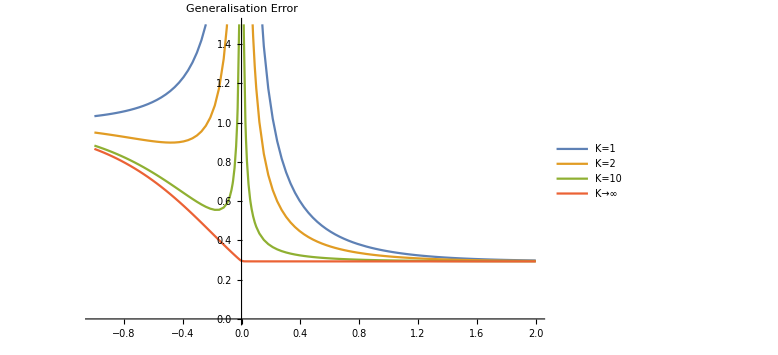
-Graphics-Log10[P/N]

```mathematica
genPlot["pts" ->{ptsVk2,ptsMk2,ptsMk10,ptsInfk2}, "plotRange" -> {0.0, 1.5}, "xaxisLabel" -> xaxesLabel, "yaxisLabel" -> yaxesLabel, "leg" -> leg, "colors" -> 0, "legPos" -> {.82, .8}]
```

```mathematica
Manipulate[plotk[k],{k,2,100,1}]
```

## Figure 6

### Generate points

```mathematica
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->1,"λ"->10^-5,"ψ1"->0.0];
(*in order to obtain more points around the interpolation threshold P/N∈[10^-0.2,10^0.2] *)
{Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin}=plotTermbyTermEvol["ψ2"->1.0,"plot"->False, "NbPoints"->50, "minVal"-> -0.2, "maxVal"->0.2,"λ"->10^-5,"ψ1"->0.0];
pts1={Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg};
pts2={Ψ1fin,Ψ2fin,Ψ3fin,Ψ4fin,Ψ5fin,Ψ6fin};
{Ψ1,Ψ2,Ψ3,Ψ4,Ψ5,Ψ6}=Table[Sort[Join[pts1[[i]],pts2[[i]]]],{i,1,6}];
```

### Data

```mathematica
(*lambda=10^-5 psi2=1.0*)
{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}=Uncompress["1:eJyN3HlYTfkfwPEzNFRKjSmMpa6thdBYky2E0LQYmcYyomWahFxJFK6EUCQZaZlCRpqYJMqSe7UoCmWXVFoUQiQT05jfOff4fc/H/Zxvz9w/5nnmeT/3nnPP/Z7ldb5HfZasmO3RgWGYVWrsf2x/WeXrsfqz/2sH/0/KKF+NcuneHcH5ye5pE1W6umFg46WOr+TS4K6TEi3STql2nQktlZt1Xsqlq88eexylf1q1d1/oWzK12wu5dNS1Tpes9pxR7cqPN2yQS+uPV+/NNMpU7cYx3mlXjJ7LpTm7mwtj7p1V7UPP1R/aOeSZXGqw+f3NqCPnVfuoB257vxv1VC6Vzc6K8YnIUu3K1Z9QL5fur6962BwvV+3TunFfoE4u/crymxdf1itUu51yAU/Y9XOtWTC7S7Zqd1K+auXSuE3f7K2wz1Htys2zsEYudZlXFX/yYK5qd2fX/oFbtVzaS0Pf8Yb6ZdXObZ0Y7yq59EzPrJSJW/NVu/LjfR/Lpfui1a526HlFtSs3f2ClXBoamtDQp+Cqau+o/IEq5NK6I+a5QbuKVHtX5Rd4JJd6VH88obHiumo3Uv5+D+XS1l1eKyaOLBb/fR7IpbOfqUvyrEpU+1Tl9r8nlxa5t7R3mndTfPvekUsvVM1u+Drolmp3VW6/W3Kpn6Hh+A6Zt8W3T4lcmnhUU6LReke1qym//w25tFF968DC7+6p9v7K71col+qtDziWm3JftVsr1z9fLg23Udwf2r1Utbso1y9HLj141Nb2i90Pxfc/uVzqtnvYmkqdR6o9+gD3OiuXFnital7ct1y12yiXnyGXev66bpbBAdTXL9/+vbzujFzqMMXI+/kfqP80Za127ch0udS81HHoiFEVqt2q+y/5msEn5VJvj7E1kkuoM8r1/1MuPfS8/XQ7vUq0fqUn2y1OPC6XltqeabQxQl0reI9filWSXFrja1ky1Bv14sErn/1VdojtN7bHm6ShXmnALT9eLtVNb54U+Qj1gX8evLD1TTT7+425ve7jX6ins2vXe1C4XJp0aWhuz/GPVXuL8ybzm7tWs5+/VdvLdAPqn94/UcocubO04nfUTfjls/3Muz9/SEJdotx+8WzXjDuaiPs1/vuzPcQ77V/cNfjtx3bvP2x+Oob6p+3P9pT8m9G488v/k+3pyzSO4v7p9+eWH1aai/un8cN2iy6Z1bgH8uOP7W9bnf4WWT9+/LK9SL3vR9w/jX+2ewb8rZ2M+qf9h+2NHummuHvy+x/XZxZOwd2W33/Z7rNH4oS7Gb//sz3hxqrFuGvxxw/u85ce8cLdjz/+sD1VpliJuwd//GK7rqf7Gtzn8sc/tjMWHwJw57ffPbYXf5mzEXdL/vjLfb+/XgbhPpA/frNdkRW/BXf+/P6I7TKdl9tw1+TPH9z6rWnYjvt6/vzDfX6/YztxX8Ofv7jtZzA0DPfl/PmP7ZWG23bh/un8yW1fSeZu3Bfx51+2OxTkh9O2by3bJWfO7cHdgT//s908KzIC9+n89QPXtX/ci/un6w/u8+doRuJuwV+/cNvnbrJIN+Wvj7jv3+7SPtwl/PUVNz6zx/yKew/++oz7fZgkkf4Vf33HdqsbWvtp+9cr7vP7/iLSv2C4VyPbXa5niXT++oPrirBOUbh/4DZPC9clHb8X6auV4+M1t/xrkSL9jfLjuc64l4h0fvy84dZvssYB3J+yV5fn6t8ov/84kc7vn01c9/IW6VXc6ldyPcEzSqT/pBx/b7nld7sk0kuVuyfXK88/Een8+GzmPn+fRjTuN5WHF2V/ZCrS+evXd9z2KZgu0guVF3BclwW7inT++vgv7vtPWC/Sc5UXkFyX9N4n0icqx38L16f+IdKVl/fnuK64Jxfp/P7xntt+TTdF+inu503jOpNeI9LNlQv4wK3/8GaRnpLMvbheGaIWg7uJcv/7m9s+V7uI9ERu+BziukJLItL5/bOV64vNRHqs8gKf6y6lo0U6f/z9h1u/rZNF+j5ueO7lOuNnK9J1lfv3R258pDuJ9FBu9XdynXH4SaRrKPf/f7n+vYdID1YCkeuKgmUineFfVuzvf95X2f+TVuefn9Zf0wNpiGjVbIdxu8caBVSt7moyCux9DWmIaFX98IKw8WmFVK0O++GX6A/nr1G1WmitN9jxxQ2qVof9OdAgrz/SDtFql23LRvfzQtohWp2w+HhzXgHSDtFqt9bqi88nI80QrWr2OK77zcO7VK2mdPUYbhSJNEO0anbz8GOHlUgzRKuRcR/nfu9XRtXqwRFupUFHkTaIVgPGBbq3BqOrcaLVW0einWpL0GgiWo19cP3doAnVVK12mJL3bv71GqpWzarVrcxCnlC1miqJeNAkradq1WuDR+i8qGdUrV5+rX5k6ZcvqFpN3z3nun3RK6pW7ZbHGUZtfk3VqvVmn5OHlzdRtfpy2InCAZebqVq12LSu06GsFqpWPX+u1397spWq1VQjo5krhnxhRdPq/ZlSNZ2uaqqdaDVhbMEYz4wvVTvRqou8MDiO6aDaBa3OXKrn56Gu2olWXdQj1TI2dlLtRKsKP49KtTWd0fr9X6uybWE9/FN0VDvRKnNWfXPpjS6qnWhVpqFpVPRzN9VOtMqUnCi5kddTtROtMv62ktXehqqdaJVJXzT4gaOJaidaZWTZ72YUWlDezx3No65kOxqrdkGrTPG3tgG9VbugVYbZNab0G9UuaJVhfLtv0VftglYZxdrOf+tStr+yh31roCW+fE6rjGzohVealN9f2Y9u1kLjQ9Aqw6ww74zGn6BVhvExzWlHGb/K/lP0etQFrTLM7dlNjGoXtMperqwIQvuXoFWGkcQt/4uuVfZy7mjnt3StcuufhI4fglbZAeBzHh1/BK0yTGzmuwa6VhlGXZ6Djn9Aq8yFnA/o+ClolT3LT95UR9cqe8lQYY2Oz4JW2ddai1q6Vhkmc8VsdPwHWmXebt+Jzh+CVtn1syqvomuVYWqmT0Nd0CrDeI5RtKFVdoAunNGGVhkmWFaBzo+CVhmm+x0Z6oJWGab10SDUBa2yr3MX0d08Qavs9t81AnVBqwyj65uBzu+CVhkmNbEc3c0UtMowldtkqEOtFscMRF3QKrt/aJSh6w9Bq+z4/zoSdUGr7O+jPxt1Qavs9w/UR13QKrv8/Efobq6gVYa5H5SMOtAqYzEjAHVBqwzjctEedUGr7P4bboy6oFV2+69uh7qgVfYAO6gSXd8JWmW3n58CdUGr7Pg1PIy6oFX2923ehrqgVYZJKlqOOtAqExXwA+qCVtn1ezQJdUGrDGNTPBh1QasM4zyyJ+qCVtnlN2qgLmiV3b517x/QtcruH+2fow60ytSbPUJd0Cq7fo7FqAtaZZiEhbmoC1plP9/qLOqCVtnf7/kJ1AWtsu+3O4K6oFV2/1wYi7qgVXb/0IpEHWiVUbcLRV3QKsNYf7MFdaBVxsJtA+pAq4zvAH/UBa2yx/85UtQZ/mWl/P7PvB/8R612X6TzMHPlBapWHwbPH2Ykv0jV6qqraQ9fJqC5R6LVpu8tl9769xJVq521g3bu2IjmHolWLw/ONr7bL4+q1cEmZT4dXiNtE63uaLyop9+AtE20mqC/ufVyD6RpotWay3v9725GmiZa9YwpHRnZDc0dEq0+rZn0oeNepGmi1ZfXdU/fHIO0TLR6ujEpI6YL0jLRqna/vx+uGIDm/ohWzSuqU/sHotFCtJo6xSyxvC86WxCtVvruW3PFBJ1NiVa37Bo9NswBXQ0QrUY8X3jYaja6WiFaXXpm0bKDx9DVENFqQj//u+be6GqMaNUjrnX8xIznVK1qfZWde/MUXase4b189tq9oWo1Y+rtcjUPpFGiVe8TWvbv3d9TtVo5bJRnePZHqlZ3fHFrwDSj9pSrbVaDq/PCbG4iDRCtJkyYe3fOfazB/2vVwfSu5fn+X1G1mtlsX7xaijrRqueI9qMC2+nRtbr9YUD7+UiLRKuVNgHGrvt60LXqGOGysw5pkmhV99nAvYMt+lC1WhkTMtnU1oiqVUXjvcEhAwZRtSobbjr1ysihdK2OWpRZMXoMXas+0ZqyGzPb0Kq0adoO9H6g1fs9h35EywdatVmzswmtP9Cqf8IrQ6RhoFXJ0zLdvm1p9f4/cRQtK7UquZ5l26sNrbowXnpI01CrUxRZSNNAqxKXD0O+bkurpq6P0d0KoFWrheGmaPwCrcru/GCPNA60Kuv49RF0twZq1bfjY6RloFVZL7vhSMtQq6HuPyMtQ6329XNAxw+oVca07F1bWm3sV440DbVaX2yB7rZBrSpO3kPahloN7pPS2JZWnXPmouMr1Gr/vGh0NxFqNeVNN6R1qNX6tFykdahVk5UHnral1e69wtH5A2o14cphpHmo1bJVxUjzUKu++V1Qh1ot+vgzOr9Brc7Ju4a0D7Wq1Xcy6lCrsX0c0PkVanWcfh3SPtTquMHbUIdatVk7FHWoVca4oo25VXb7rt/Xxtwqq60Hjm3MrbLj74+v25hbZceXtBTdLYBalZ0/gjrUqnOf1ahDrfa3sUEdalX2yAD1z7Q65DW6foJatXBPRh1qNbPWE3Wo1e6TzVCHWq3v+hbd7YBaddBQoA616n95N+pQq+btXVH/TKvrxqAOtcq86II61Kqkzyt0NwVqVfH4GupQqyYfT6AOtZo6IwJ1qFWTmDWoQ636FP2EOtSq4tx0yt0kXqNJU4ehDrXqbG+AOtRq0oVOqEOttqz6gK7voVYTFj5DHWrVxu0h6lCrzquuoQ616uCvQJ3hX0qtqi9JL/uPWr0T/2bwiAubqVpNP5zUfv/mrVStmo0/a7znj+1UrT7Z7nhqtVUYVasxHXQffzwaTtWq+8DSPafeRlC1WnV72h9Xdu2javXUkqGd926MompVd0GvxY4lMVSthi2zDJyyO56q1ctvO6+6X3WQqtWfM+MmvrdKpGp13UWbxLFPf6dqVSta65/F1ceoWu0anvvq9OjjVK1qOp2YJVuTStVq6A3JyQnb0ZPgRKv2tcljq++kU7X6e/7g5AVLMqhadb2bZnhs+DmqVm/tnBJ60Q49qU20euHszpBRC9DdEKLVLXOGuMRZoiexiVZdR+T0jbVGT1oTrbr8edK4LgDd7SBavffFRLXsx+huB9FqZFhtdoUfuttBtOpoNa/Kaix6UppodfQwta/U96O7HUSrQwyaZ8mN0LMBRKuW8SOv6cxCdzuIVjc0PEn+rhB1YW7V5OXk0xWoE61K6kPOHPBDT1ITrda0ux/xmw66m0K0GlW7zy44CHWiVZus7Y7xyagTrZrP8LRbNh09u0C0yqxcF51bizrRaoL/K+lpG3Q3h2jV6kqusfEW1IlWZfcWBQzvj56NELS6YFJjl/OoA60Gxur0wPdmBa1aHdjYG997FbTq89twA9SBVm0i1A3xvU9Bq403a3EHWjWXrpJQlq/UqlW7cNyBVisVd3AHWpW19u6D75YJWpV964Q70KrVpfm4w7nVYhnucG41+RLucG414yPuQKuyKcZ9UYdzq72tcYdajfkRd6jVkV64Q62OWoM71GrnINyhVj/uwB1q9fcI3KFWpVG4Q63O+w13qNWqQ7hDrfY/ijvUakgy7lCrbsdxh1odkYo71KrkFG378lpVP4071KpJBu5Qq/WZuEOtFp3DHWo14Tzun82tXsQdajVUjjvUqr8Cd6jVhku4Q60mZeMOtVqWgzvUqk0u7lCr40Q61OptkQ616ptHGz+8Rt9exh1qNVikf6bVfNyhVm+LdKjVcQW4fza3KtKhVr1FOtSqj0iHWu11BXeoVTWRDrWqexV3qFVfkfdDrfYSeT/UqoVIh1qtF/l8qFWxz4daZQpxh1rVE+lQq+oiHWq1TGT5UKu5Ih1q1Ufk86FWw0U61KqZSIdaLRDpUKuJIh1qNVKkQ61qFeHO8C+lViXK/p+0etY5om7JlNVUreYqpub94+pP1+rCdNcl7wOoWs3660frkZoyqlZXWvbuNMgtiKrVxOyeh8P1t1C1ukjvjW/TwBCqVhNSFg5JSttJ1aqiri5UM2s3Vav+BV6arkOQlolWbc01AyNvRVK1utZvvv2k0v1Urbp0u31uugPSMtFqqW+PxrVTkZaJVhPuDP3mTS3SMtHqRb/t8zoHIi0TreZUbZt6w+coVatFQYc2R5UkU7X6oix044njJ6ha7e5k+cO4nSepWp03LlXviQ7SMNGqdnx5qGEj+nfPRKunMsbFZFsgDROtHlnfI8yrBWmYaHV6TqnLHUM090+06pJmYZAYjub+iVYj7F+YWv6ItEu0mqlXlxK0BT0pT7Sa6er04FZfNHdPtFoQOPWLf+ORZolWi8dm3X5niTRLtKpYOSMn4R3qRKuNFRvkz/ToWjUxOBWf1II60Wrq0RijXU+QZolWE5waZE1xdK3qqh3b8bacrlWHhoxJJlV0rVYeGv/P7EakTeFJ4CSXFdFxSJPC3OqwOa7DNdDRVNBqn+UjSwaiJ5UErd5vUN81DT0JBrTqPKn8H9SBVi/MjFBD9x6BVp03vf4SdaBVn457OuJ7n4JWXW5ZaaAO51bHO2lSlq/UamW7MNyBVq3M9DuhDrXa9xDuUKut2lp4/QStyvJ64A60qhjoijvUasFj3OHc6htnbdTh3Gq/JNyhVr0qcYdaDdDsjDrU6pOBuEOtplnjDrUa+yPuUKsNXrhDrXqvxR1qNXEL7lCrE8Jxh1qdfQB3qFXrg7hDrVol4f7Zk8AncIdaLTqFO9RqSiZt+/Ja1crCHWpV7xLuUKu+ubhDrQbm4w616nYVd6jVBTdwh1q9UII71GrILdyhVhfcwR1qteYu7lCrofdxh1oteIA71Kr5Q9yhVk3KcIda9X9EGz+8Rh3KcYdaHVFB2z95jZpU4g61qvYYd6jVIpEOtWpdRRufvEYbRTrUang17p9ptQZ3qNUUkf6ZVmtxh1pNFelQqwUiHWrV+Qlt/+A1minSoVZbRDrUqkUd7lCrziIdatVfpEOtMvW0/ZPXqLlIh1p1EelQqyEiHWo1SaRDreo+xR1qlRHpUKti74dalYl0hn8pteqi7P9Jq1EfDK2nGdO1qp1teqrjRLpW3VKXrLleQNdqRsCes1G3N1K1+q/nwswplnStzno60Di8PJiqVe3I8rtXq7ZRtTp2h8tEzTl0rfqcOfi20yS6VhM26W41f7SHqtX9ZR9m2f1C16r7jIVnJ9nTtfret6fBb9HRVK2mfXulZYLzb1Steo7VvzhkFl2r2jt6r3BMO0zVat+0MwU9vNDcLtHqzdSWTRUBaG6XaPVWpd2qU69TqFr9UdFFz3wpmtslWl1QvrvrsWg0t0u0emaG4fTx2uiveBGt2jT0vqN7Bc3tEq2O17AzmXMbaZZo9UNAxNc9RqIn3YlWE0bWDdrTguZ2iVbzr+rkFXZAmiVaLZBMVXeZjp5kJ1pd7jTfuuQ8+itZRKvZTw9mXndDfwWLaLWmLCwu1gX9FSyiVR/bOWuaJyENE62+jYzXbnZHnWi1u3u/BpeVaG6YaLX+tb59VhD6d+VEq7lzLb4/Y4K0TbRqIjNf/8IWdaJVhUeoydiHqBOtKtY7d/zKGz1pT7Ra6VDXfUA+6kSrihkhl5l/UReeBN5/zS03Amlf0Oq0ztc/GCLNA63OHfzzWtSBVs22HwlEHWg12Nt+PepAq/fdum9AHWp1xFPcgVYTypZvpCxfqVWHW9txh1pNKsQdaFVyXUeGOtRq0xTcgVYTJDNxh3OrhstwB1pVzE3GHc6tNlXjDrU6WnMT6vBJ4JUDcIdaPT8Gd6jVZTNwh1qtdsIdavVLF9yhVhd74g61umQF7lCrdqtxh1r1XIc71GrxBtyhVhODcIda1dyKO9RqYwjuUKtRO3GHWm0Io21fXqudw3GHWn23B3eo1cS9uEOt9t+HO9Rq5K+4Q602ROEOtcpE4w61WinSoVaLYnCHWo2KxR1qdU4c7lCrzG+4Q63GinSoVbN43KFWE0U61KokAXeo1ViRDrXaKtKhVj0P4g61qhDpUKuSQ7TxyWvURaRDraaIdKjVFpEOtTriMO5Qq54iHWo1VqR/plWRDrXaKNKhViWJuEOtWot0qFUfkQ61Gi7SoVZTRTrUapFIh1otFulQq2pHaMdfXqNaIv2zuVWRDrU6QqRDrS4Q6VCrPiIdalWsM/xLqdVArv8P05y4SA=="];
```

```mathematica
Do[
{varIn[k],varNoise[k],varData[k],bias[k],tot[k],plotDec[k]}=plotBiasVarRatioEvol["legPos"->{.825,.8},"ψ2"->1.0,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"λ"->10^-5,"ψ1"->0.0,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 1.0,"k"->k,"pts"->{Ψ1lowreg,Ψ2lowreg,Ψ3lowreg,Ψ4lowreg,Ψ5lowreg,Ψ6lowreg}];
,{k,Range[100]}];
```

Set::write: Tag List in {{-1.,0.15398},{-0.969697,0.163621},{-0.939394,0.173736},{-0.909091,0.184328},{-0.878788,0.19539},{-0.848485,0.206913},{-0.818182,0.21888},{-0.787879,0.231262},«36»,{0.333333,0.144969},{0.363636,0.134803},{0.393939,0.125319},{0.424242,0.116481},{0.454545,0.108257},{0.484848,0.100609},«50»}[1] is Protected.

Set::write: Tag List in {{-1.,0.10314},{-0.969697,0.110739},{-0.939394,0.11889},{-0.909091,0.12763},{-0.878788,0.136994},{-0.848485,0.147019},{-0.818182,0.15774},{-0.787879,0.169191},«36»,{0.333333,0.367712},{0.363636,0.358963},{0.393939,0.350614},{0.424242,0.342677},{0.454545,0.335155},{0.484848,0.328045},«50»}[1] is Protected.

Set::write: Tag List in {{-1.,0.0042064},{-0.969697,0.00475056},{-0.939394,0.00535809},{-0.909091,0.00603485},{-0.878788,0.00678685},{-0.848485,0.00762022},{-0.818182,0.0085411},{-0.787879,0.00955549},«36»,{0.333333,0.0675815},{0.363636,0.0680445},{0.393939,0.0684671},{0.424242,0.0688533},{0.454545,0.0692065},{0.484848,0.0695298},«50»}[1] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

### Display Plots

-Graphics-Log_10(P/N)

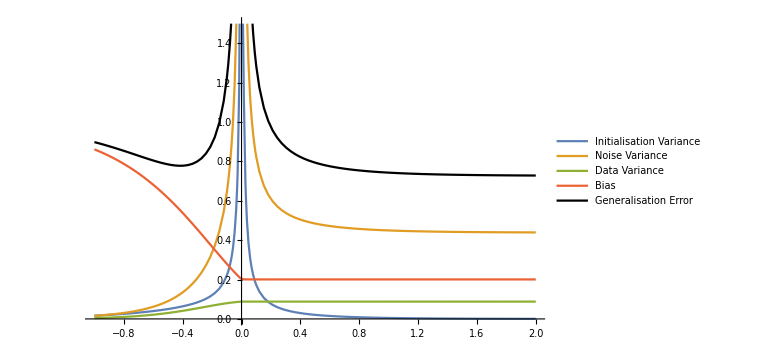
-Graphics-Log_10(P/N)

```mathematica
plotDec[1]
plotDec[10]
```

## Figure 6

### Generate points

```mathematica
{ptsVk5,ptsMk5,ptsBk5}=plotmoreVsbig["ψ1"->5.0,"k"->2,"λ"->10^-5,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,
"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 0.1];
{ptsV05,ptsM05,ptsB05}=plotmoreVsbig["ψ1"->0.5,"k"->2,"λ"->10^-5,"plot"->False, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,
"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 0.1];
```

### Data

```mathematica
(*"ψ1"->5,"k"->2,"λ"->10^-5,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"F1"-> 1.0, "FStar"-> 0.1, "τ"-> 0.1*)
{ptsVk5,ptsMk5,ptsBk5}=Uncompress["1:eJyNmXk4Vfkfx+9IScugiJYJQ7IlpYxKTtPGFNMyjdQoiW4aaTjTQrdSthE1V5NKVMRVKtugbNW1FVkyhuzKGrJkbImW37nn9vvM/M7Hmed3/vA8ntdzlu/3+/l8z+t9rurunzZzx3A4nJ8lqT/m+34+yN31P/9J/PM/kkMfPUJSIfbxV7y0LoLBxysf68mUei0keYGG1yX8EZcxGar3lOkWkoNtmxMWWCGutONgyRrFLiF1I6XwIlXE6csrdwpJrVqBZHBrJ5PPDdmf8ESjQ0h6Oy59uuUW4vPT2sL99V4JSYF+2Jk0LuKGVfbnLQzbhaRBouzVU8qI049v0iYkgy9/J2Vb2sHkaxVFA2gVkhMu/TBzvAfi39I3eCkkuVzXaHUdxL+njxYh6fJ+57bdT18xOT09O5qp8VvfWuvgiLho9CH7G4VkbK4wZd+5dianTz/YQM2/5o3f46YjTk/vsXohmT0wxnBrcBuTj6MX4IWQTHlu6zlxKuL08BXrqPMPTdI87tnK5Br0+tQISesN5Mw9HS+ZfA19gQoRVw19GNYy+vw8E5Im+Vn1fV3NTG5HrV6VfSl1Pr9h+YKFiIvHX0Ktv7PV/AinJiYfS4+vWFR/Bk/CwhqZfBd9/WyqPvq6wjwn149e/0IhqexdPmJg8ZzJTenxJVP9o3feaJpbLZNz6PPjhGRAVkrJifBqJq+aLeKhVH1VbDHKLqpk8sktGgq8ghBjqj53PbzysZzJ59HXDyVIlwdvjo8YP2NyFfH9Caq/41wK/UpHr+9kgqovh9q7XSUs4yeo+bv4onTfH0zuIJ4/0fWvlw9LPmVyc/r6uQRZVOh4yeBgAZPr0PVTILr+pB0z1Z8w+STx+hHkxIo0S3eFXCY/LF5/gvTpWPSDg+kjJueK64cgU2e/5rskZzO5pbj+qPMdr95ZsDtr9PWtoMan9z4yclUmky+l95cqgrSWWekXuDWDybXF/SEa38EDuQbC0ffHOtH5IWPvTX7I5BPE/UmQWYdmJSYaPmDy4+L+Jkgz2zudkrfvM/kR8f5AkJURhGaWPeIHxPsLQdWfRKEOF/E99Pw1iZ4vPX1GPOI24v2LoPpP1jfSFD2feH5bCPJpodpJdUM0vo3i/ZPi5gYLqv3Q/Ijnv5W6P3/e9hexaH4/7d8Eqf3Obu+CV2h9jMT7P1U/yX4zD11A6//p/UGQe2/sNCtoRPWjJX7/EKTKnl8Ne7VRfaqI31/U8xsrDccrofqfIX7/Uf21ar+ywueo/+TE709qfdS0yMt70P7w6f1LkMELR3469hfa/z4Tv78JMihcpW3D0e7R93+Kd/3h5a/mjM4fFk3fEMU3TPs8yfpGFZMfouvnL4Ks+uHbrpY9fzJ5L315iqf+GjPrRUHh6PXVS5DhTWSsZDHq33Zq9tPaKO6ho/adlFPO6P3bR5D7vpKtKnuP1rdR9Pj1FJ/ReTb8gBaqj510ffYTpOsOXsIXPFSf1XT7UrzyptfFIcP00et3gCAXSevf/3NnKpP/SW8/FO95+8RmbGXy6H4wSJDXHPviRvj3mLyAfoFS/NtQ1VU73O6Ovj+/IcjqdypJ3/slMXmOaPozKZ5QHPXyRHoikxN0fwxR+0+Zs5SuFOJ0+adR3JNjrNfjkDB6/7wlyPILGt3r6n5n8kTR8iZQvKA7OMHJFnF9+gbDBOkcZ5cq1xfP5NG3RQfF1905vX9bAOKadP+NEOTFM83RqV8hLhCVTzjFly2NOlVSHDd6f74jyMYrf90OJxC/QgsWxblWPYOyD2JH35/fU/0d05nkvxbxC6LyPE/x60M3Z6VXxzC5LN3fHwhy/L5S/mFXxM+IHt+f4poNhoX3ZyMuTff/R4J89k35tZjCaCb3ogWc4pPy5+d4nUKcIz5WkEKi++4FY4rv/CdnSwNa1kc6TNPZ00Dj8KWF3f+SBsxsVVcR29jTgEJ3l6mEGnsaaBgushhpY08DLsu7DNpvs6cBTsbYbF8H9jTA1RiwPK/KngaW5xfde/iMPQ0clc/fft/rX9KAxuOTy/TY04B3R1FTewmy/U9vW8o219zzPTKOPQ0oP4pdFnWRPQ1wb0xRuaXMngYGoqr95lxnTwMCfad9+TPY04C3o2vM+jPsaUDQs0ebO4DSgHj+q6g0WSZZ2vQ94pAGiiY5fe3/jj0NbDZq25i0EvG/bf/k0t8S77LbfvD0mQZXdZDtg83zAo0H+3PYbV5e77G59xt2mxf0GAt6ddHbFGw+QCK0V/7HClabVx4b5cVJYrf5WCnnLcUyZaw2Lx8rb2fjgd7WYPMTFX2Tp8oi2web17LmzzB2K2a1eV7g8LkkhSJWm+8oKavxfZvPavP8rPBeubnIpsDmL1/OS7MLRbYANi9wbjUo3f2Y1eatZZ5Nj3NBNgc2r12bEaFUhGwDbJ5zUq5P3RVxsHnvO3VT9rohDjYf4LFPbUMd4mDz2sZ1X5iloecDmzc9Fb400AiNH2yee2O8w+QINH9g8z53om038dH6gM1zrDbJrp+L6gNsvvMbzb0v01EaBZtX/qnN4oQX6j+w+Q+3pL6USeljtXl3s76RGzXoawDY/MptWR9+GUb3B5tPUNC08D2P6hdsvnnp2bdWJ1DaBJu/UauQYVWN6gdsfpJH7vyrGSgt/G3zitJdG/yQjYLNx2+xWJX5CKUZsPkgh4fx/YuRjYLNJ2mWOevqIhsFmw86tD/ngyeyUbB5wdHX5kpzUlhtvuymaVvwB2SjYPO7mpdMOyyJONg8J+b64qfzkK2CzddPnBH07mdkq2DzxlOOJrSXIBsFm09aNHT42irEweaHboefG3qEbBVsfqPa4q2HLBEHmw8651Q5sQ/ZKtj8/WWS6+SCEQebDxCuvqq+DnGweUnFXn1lCcTB5p0VfpsnnYlsFmy+P8whQNYHcbB59XJjA4+NiIPN978q3JSjjDjYfNSlDFvBS2TDYPNtOg1rXS4gDjZvVnL5iMZ6xMHm65+vGCcvhTjYfJB75uLQPGTTYPNWT+7ZE3zEweaNhue687YjDjbvK51R26rFbvNGGz87ov4e2TbYvMOStXtrStltXsXu91BhDLvN50lklfn7sdt85ZZV/M9+RBxsnnOvwaZtPeIc8bGC1HR8rTdZP+b/tPlBzdV5pyegbwNg8xVq/Usu1LPbvInf8fyIRHabF8Q3xbt7stu8oGfQpXcD4mDz1vzI3Q+VEAebz76r9yayjt3mFQ6UL+ZeY7f57LvKFanbEQebLypsy7WcgjjYPK9scvjrHHab79y0aJ0hiTjYvNas7dK8dHab50ukcostEQebz178zI3XwW7zRebrd2m7IQ42r3DgiMD3I7vNF5n3fWN2AnGweZcHC0+rDiDbB5tvWOpYU2WHONg8Z0VYgLkmsn2w+cGoOa29x5ENgM3H5s6sfS6LbANs3tux1FcjpYHV5gXxXnoGssj2weZjc220xhxE3/bB5mNz65Mt81EaAJtXfhS4xUSzhtXmFfQko1t/Q2kAbL7C7iMvRAbZDtg8T56X5hmBvv2DzVc0lU048B1KC2Dzyt4dZSFqKC2AzXvruCqFK6Jvk2DzFU0nZLkLkS2CzWvVRvoYHUY2BjavVevzRrYF/XYANj+oKTen/STiYPN8CfdQY3PEweYF+uUmCesQB5s3ux4hPcEDcbD51A8TNE6NIA42b5aZEzDtMRof2Hzn1543zw+j+QGb19I9snJXNpp/sPnNlZeeLXNCaRBsftC3ZOt+PqovsHlBrVqmmQmqf7D5xovVt3a/RP0JNl90+VZgr2o/q81fqbcY0316zAo2m8+bnffaxmOA1eZ3ere1hK1H+wvYfFC5tERaK+pPsPnYYytmr9ZFaRtsXnH7zYA1Z3Fa/q/NOwozFkx3ResDNn9bWHh0cA1af7D5BJ6PXPxqlKbA5hXO1U5rTkdpF2xev/yOlH9KHqvNN9jUlJtNQ2kPbH7r1jrD8vsoLYLNb3xhn2YTgtIm2HzWsWKn55EozYDNP1lycrl7KfrtC2zeemKvdsQXiIPNV65pCVrizv5tPn1awf1N/ezf5kMJqddP3RAHmzdST79tMBlxsPmUXjebN1YobYHNG/r5dHOi0W9PYPNGB9XinsgiDjZ/9OKXxyd6o7QGNj84YjqvbhziYPM77TYkhAWi387A5u/tKlgyoIs42LwEv2ll9FOUBsHm8+XGvMlwRRxs3nLP+eWbtBEHm69Mi9UIakxjtflxqWm27WGIg83XHpf5JcYecbB5jQB9aZt5iIPNN+//PPqXYZRmweZPTjV2eFiAONh8s2VUZGQY4mDzBwZTHrS7Ig42r7tjIJnYgjjYfFLdR0P7hYiDzZvIXD07YyriYPP2MTMHdAZRGueIjxVkXlPMC25NCvEfkW6O6A=="];
(*"ψ1"->0.5,"k"->2,"λ"->10^-5,"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"F1"-> 1.0, "FStar"-> 0.1, "τ"-> 0.1*)
{ptsV05,ptsM05,ptsB05}=Uncompress["1:eJyN2Hk0V3kfwHFFkaREGJNos9RQU0085dcVk3nMtKlUtqIsRSpfsleKVLSQpPxQkRZb0RCSH1EqlaVpw1iyFiJUkuW57u35nHnup985z++Pzum8Du7ve7/33vfnTt2ya429qIiIiKsY/c/y7a5u9jb/87+R//wfEWE+nQJiOb48KsCuk+K4hIpvZ754h4CcjHWWC3NCPn5Jb63/+PcCkjm46rolQa5o5Va2TKFdQET8qsW/eiFnfr1Km4C43DluG3oQuTp/R9pDtVb6560PBBoeQz4nuyU2WPudgLTJmM3gRSBf+No2bMXCt/T36/g9Nj0OOXP4S1poX2Xk3Z6K3Ehh+As003//QlbDnLvIVzJ/oElA1pxt5FX8hdyU+TTS32/AcJ7VO+TM8lg10MdfJjBaKvqB63b00b+2rReQS6t74+eqIh9eHf6ON/T655qG9C9Fzvx6tzoBqTMPa03YjpxZft/a4eP/lBV4Fvlo5gTVCEik2XHd+aXImeVR+FtAnkiNM346sYvrasz5qxSQ+fV7/1Daipw9P68F5OX8Hc9zC5EvY/7ASwGZtPOPyit63d9f3+f077855lBkGfKtzPo9o49Pj3dZ5XjP99enjF4fpfGfxu79yPVRzPcvod2xzG12xieuz2S+X7GA8H7/wWOeWS/XDZnjLxIQFefgrfyoPq5bM8dXQO+P9voB4zcD37/+BALSmtzanOU+Qp97/TJ+nXYL93AFV2muazF+niKXdyn4ecz5keuq7M9TZNWaAet8fymus/v/FkX6zZMl21JFuf7t+ChiOPG3oeKgQe7xb2O/H0Vutix21eZ94fpydn0oMlriZPa9DLT+s9n1pcizmQZn3i5A51eKPT8UUfKeYjh2Pdqf7uz5pYjczuSrRUUdXLdn9wdFxuZaW/7p08719ez+osiYBeY9G2Jauf4buz8pEmqcd15E7h3XF7H7myJWz6Wv7X/YwvVZ7PVBETXFtbUqqc3fv3/+TZEVIbMflec1cV2SvT4pwi/QzpH60Mj1vez1TZFFzp7t4nrIPdj7A0VU0+M9jaIbuL6Tvb9QJIWnP01PBvm3+xNF3DtM+mTC67m+mb2/UURduWixjxpydn0bKTKipaQ9vOAN11ez91eKrBc/cPOZI3J2/ZspEpIv69CihPzb/Z0i5Sc963LK67iuyz4fKOJslvzUNhT5t+cLRVI3uRfKr0euyT6fKGL5tF5STRW5Kvt8o68v6Y/JA+9rua7EPh8pkrglOHjyXeQy7POVIhWL0mdMPIf82/OZIo0Hw8V9XZGPGH68i3RSJELncKqoCXL2/k97kvntUsufkfcNL18v7ZEyuuWGcsj3MPvnA0Wu7c8x/9JVw/Uu5tfTHqkVdzcuHzm7v7ookrV2+kL108jf0quf3UL7xpj2L1qOyNnrt5sigVf2iDoZIn8zfPi1tJ8tSWs7q4J8E7M/e+j7W0D3OK/Baq5XMJcv7a9kwm6V1yBn9+9HikzW2RdICpCXM7cf2i3jrUo0ryFn++ETRZTHfZz8NAR5MfMApV1PoypX1xs5e3/+TJGFA3PtjeyQFw4vfz7tT6SNnr4wQU4x10cvRX6ee3HXYwo5s/2zaQ+wqlssNQc5e/18ocg6P0ubvSrIbw6f3jTa/2W2e9IYGeRzmT/QR5EL0xJtI0WRJyUMf2gPtRkvMeXz31zXYK6/rxQxiS5dcrAV+aXh7RNL+4jkocSMWuTs9dlPEen2JJ2kF8ijmMCiPSVFqXvdE+Ts/XmA9rJLQ3GFyMOHt2cY7XdmT/A8noN8AnN9D9L3J78Bi9HpyI8NH34w7QX3f90rloJ8DHP9D9H7Z4XYrn1XkAcwgU57ecJCd6eLyEXYjz6xv3TZp4BP++Z/urBpITOmvMmVL3xaCBxrGduYIHxasOxIiK/IET4t+Jx+lPakTPi04ON28aIFrmmYFkIMSscsFUc1ANNCXWSIjIsmcpgWVOL5dpPXIIdpgZewROfpQeQwLcidMA8/cAc5TAtPotbFV4qh2oVpQeVezTh7S+QwLfgsyHYYeIAcpgWfAHkjLxNUSzAt7E722JQ/hBymBc0dt9Wz3qBahmmh4CPP7K4MqmGYBgqid4uslEa1CzW+y8V6em7pUm5NQo33uayIqu2T5zrUuEJyRJrvIgmuQ423qlMPj+iiWoYa3xR2L7To0FehNR6QP+d2gd1noTXe1Xr/lcdVtD5sjdwSkJVtJyZ9/ROdH6j11HWznS0otD9eT2FqXUDab0S1nlFG+3tco9okn2K+Hmlc6xgt7/ye61D73lPM0g/0tKG73X9rn78wvE8jB9Us1L7WF7dZa9JRzULtZ/+4Ic39+Vuhtb8jx3NblRxyqH27zjPb0p1RDUPtG2911z9ZiWoYav9UXqNvlzlyqP2ZLZaZqm9RLUPt10zc6dHkjxxqv+lq4i/emsih9isLq3favkI1DbVfrhzY7HwSOdS+Y/9Nm1MrkEPt97hJHvgkgxxqv6XLdGRtJapxqH0Xgy1J1xOQQ+1nvnocXLVXeO1v6heb1blOeO0XenQH+M9BDrU/8lYNX28ccqj9eYlDux+3o2kAav/RodEO7aXIofazS0ubbTKQQ+1bFUUv645GDrWv83p/8e7DyKH2nVSn9qQQ5FD7Zx1eCAI3I4fan8pzmvF8BXKo/Sm22qe8ecih9q+FxweZayOH2p9L+pdZqCKH2o/JK7G1k0UOtZ/YbJO0VRw51H6/XEyxQT+apqD2+yaeU//wATnUvlSSa8qmFuRQ+y0W6dd9a5BD7XsXm2XxXiKH2jfRbPMML0EOtf+X1/QLng+QQ+3vTAx6XJWPHGpfMarEJfM2cqj9Ot6W+yMzkEPtnzL5Me3mDeRQ+37SibkFicih9rMPnxvz0xXkUPsqMQk6TbHIofbtI722t8Ugh9qPeaj987/4yKH27U1nHS2KQA61ryVxovjUaeRQ+/65QQlnQpFD7bd4btYsOYEcav9MSG+47jHkUPtSl5X8S44ih9q3DB5fEHIYOdR+562iLV6HkEPti/VsiQ/0Rw61vzxKUSTjAHKofeekPfKj/JBD7duVtWS47EMOtT/BLfzlF1/kUPshvziE8X2QQ+17G9mom3ojF2E/+kRx19TOGV5v/s/a5wXNqGzwQzUDtS+iKqmvkY0can+Norjov/uQQ+1LbsjL2miAahRqf36Y2tj0MORQ+5Ib9rV/7kAOta/pO/b9bDNUa1D79oHyzq/KkEPtr9kYGLPICr2bhNqfL2s0gQwhh9rnVWxa0H0H1TLUvs+62Hf951FtQu1HZsVP2HMdvVv+Z+3zdfrQu1Wo/flxqsZLT6PahdpXCVfYeoiP3j1D7df1LdHzUhHh1jTUfmaXhmKmgxjXofart0skXE4wEVr7cjeWbrUsnSm09h1jDx5x6pgktPb7e1NcW9rGCa19jVkbjzTIiHMdar/qhHTuZRFh77bpaaOgpal4Nfr+UPvSJXkLVZ/1C619snF5tMEgOj9Q+6/2qzyYV4LOP9S+RHV9R5Us2j9Q+xfNF7v7JqH9C7U/9U6ZxAd/dH1A7Weetm26GCzk+qZrnz+94le1LDStQO2HfVp5tFoMOdT+OqV3J+W2o2kGaj9aZov9i7vo3TzUfrJ+7PL+v9C0A7X/dtSFYH1R5FD7o244mVkYC3+3H0tSG57HoWkJaj9i8N7tivHIofZlrk67MjEYTVNQ+5n1WmuDZJFD7X/KW7A65gqatqD2nawFaa3LkEPtr3rnqvprO5q2oPZvSFU7X4pCDrW/bOAnba21yKH2Tdtd8yZPQA6175MgG/CoHE1zUPvx1Lnu2EjkUPt6P0zcM8MBOdT+0X677Cod5FD7EdavTttLIYfaF7NYOnNbA5oWofaN1zpuCBUgh9pfpXgjMjIaOdT+i1uNjw33IYfa/9B/deVaG+RQ+xH1MovCjZBD7b//OiKjQgs51P7j09tsvsgjh9rPqUksfzQCOdT+www5jZ/eo2kXan/kwfjLA5XIofZdRujaTStGDrV/zFthpN9t5FD7Tg1nbQaThEzrdM37Be1yO3weOdS+Y+p1MfEw5FD7b8vOHXE8jBxq33Lajr4LvkLeBtA1b64U/mckQQ61H2eUZWK8HTnUfs5m2ZDz1sih9vOd7uuEbkQOtd87+oGorAlyqP3RcZOOK/2OHGrf41KnTowhcqj9nozmaeE85FD7kYVeCp91kEPt+3qo+ebMQw61//Jz4W/VWsih9o2vDn40xW9boPa1lEt9lWcih9p/sf6jwZypyKH2Feo0FQKVkUPtH9LW0FBWQg61//W46UCHPHKofTtryd19ssih9m2bHeJ1ZZBD7QfxUySuSCOH2udtHGNkIIUcaj/o5d1l4pLIRdiPPomYW6XeLd5E/QcGpse8"];
```

### Display Plots

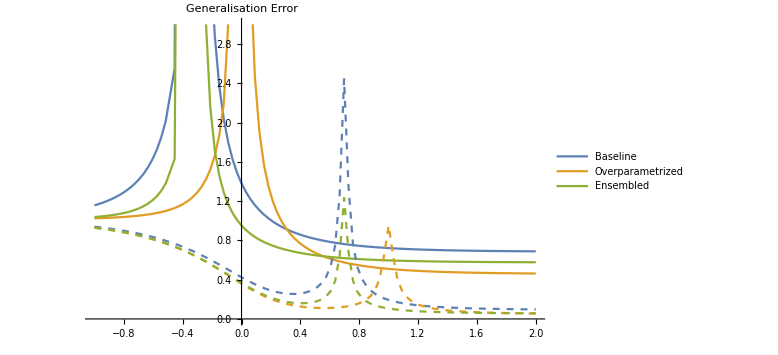
-Graphics-N/D

```mathematica
genPlot["pts"->{ptsB05,ptsV05,ptsM05,ptsBk5,ptsVk5,ptsMk5},"plotRange"->{{-1,2},{0,3.0}},"xaxisLabel"->"N/D","yaxisLabel"->"Generalisation \n Error","leg"->{"Baseline","Overparametrized","Ensembled"},"legPos"->{.82,.8},"colors"->Join[ColorData[97,"ColorList"][[1;;3]],ColorData[97,"ColorList"][[1;;3]]],
"dashed"->{Automatic,Automatic,Automatic,Dashed,Dashed,Dashed}]
```

## Figure 7.1

### Generate points

```mathematica
{Ψ1lam, Ψ2lam, Ψ3lam, Ψ4lam, Ψ5lam, Ψ6lam}= plotTermbyTermEvol["ψ1" -> 1.5, "ψ2" -> 1, "plot" -> False, "NbPoints" -> 100, "minVal" -> -3, "maxVal" -> 2.0];
```

```mathematica
Ψ6lam=ConstantArray[0,Length[Ψ1lam]];
```

### Data

```mathematica
{Ψ1lam, Ψ2lam, Ψ3lam, Ψ4lam, Ψ5lam, Ψ6lam} =Uncompress["1:eJzt2ntYzOnfwPGRpBNRUQhRmxwqZaVEE1KJSGfpJJVKoq+ElKaspI3osKIiVEJRybGYSVFIlHRQ0VGFDls6Cs/M7LWf+T3z2fu59o/nz1/XXl1c78X0nfne83nNfc9x3m3mJkSj0fYKsr9t8Njr6+byv34n8J+/o2jcL2EWxQidVrItuJHO19c4vy89FTeeRb12CKQzAlA/VpiXOEed3fXy9RQk96P+XCneK/uZEIuirTy9VMQH9QnHD+qscWb3PYOfp1p5om762Vq0YmQci5pUtVW/3Rn1GBPNGpdodnd6Uyp9wxb1qpvSaf0L2T1NY+B+zGbUp0v2+YUWCrIoU/spa8MMUbf3LVsrY8/uwhPFMveuQP1iJecfGMvul/I/6S1GvVnrJPs/dj8VP7Gzei7q3MujxO6vDzSWKEijvvO7cbAtU4BF5S31rxYWRD3DcT77ErH7gQGdHO/eBv7ekz9+dkDPGBYVEBtzSOcD6r8qfuwUP87uXqxtLRbPUd8fynmC2T3tynKXpFuo32+/9LvqAxqLslgvZT02HvUfnIdvxu5fE18obWegHsKuSZU/mdSBfLe9KdtRF2I/+vzx7P7ueo1Opj7qkdwL/INJaUWeGe+pgLoU59n3/M6k9ET2zPX9+YG/n+Nc/vhR9p+vOtI66Rbq8uq7dxiVfGNSSU7RaQHbUL/C/etHmFRyholOhCjqqg84F4jdb1CSNjI33vP3nMMpehmOw0xqoq657PB61HW4N+AQkzJdtmPvpJZ6/v6Y8/TmDzKp84nZxXp+qBuV1E6T7BtgUrZfI/ZRAqizb+67SxTZ3dm9wC86rI6/W3K/+pmUyYR+6Thh1OumcW6gr0zqUYHNuUMhtfx9G2f5uNvHpMx2PZFYNfCOv3dwXj7tvUzqWpfsj77tqO/ZwfkJ2H1cof3iqy9q+Dv38hv/yaSURKyoIBXU/f+6AZjUnT3OBknHq/m7gCfnButmUo+LZE/oNVTx98mc5SGvk0ktKTORvaiO+kzOy3P2FyaVWfhhrsThSv6+gPPwgj8xqaIbWqktT97yd23O8tDczqS2nzYLDRNBXV+GswK1ManhZrET3usq+PumJM4C1MqkhK/UqciEvuHvDpzlQbSF/fh2h4pJsMr5O/fl79XEpKaP0V7eNViG7n/uC7CBSYWbtWpbq6Iuzl2/37OvT4xiav/21/xdjru+1TKp7B4vzWGNV/x9BXcBq2JSbgIWyesuvOTvdpzl4WYFk3Jv9u+1mFiCHj9nefYtY1J5jy5cjA1+zt9li3zkinxK2M/vogD1IyPF/F2P+/7yhEl9mjIuN8K/CK2fszhPMJNJBerY7JYa+/SfX5/ZTGoxs/YX19hC/k7jPv4YJhX94Pa8uxoF6N/nrm8X6FTgBUn3OXX56O/n/vkcOrU1fbn1uSgWf2dwnx8WnQpb0Nf3MeMRf7fhvn6K6JRLWX5phnkeuj7c1/dLOhVilXz8d5kH//zzldMpr/EOcWojd9Hzw10f3tIpqRVDtwe/3ebvutz1q5pOvb0ePtQrl4PuD+76WkunHtiEpH60y0avL+71+UCnWLMnhFrkZvL3AO77UyOdOntx+2XB3Tf4+y7u+2cTnVq7/cvnsRevo/uD+/7eQqcspsb5+Ype5e8W3NdHK7uruIh8SEvl72u581EbneoKK7gWdzAZrd/s6cREs4NOXZ6g9qD84CX+vog74HyiUyZTBrOvpiah9YX7+v1Cp4zTRK+5jCSi9zfdoYYjEl10KiXpkKxo/zn+Lnib8wbTTafiWJcnRy6L4+/fYwXY/0cPnXL/sUjeIy+Wv/tx768/6dTMRVk6+oej0f3BXQB66dSvYgl9YgdO83ePv96A6JTpOo3M5nWR/L3piAT7J2B3/6UTR5toEf98/3+lU0oJy4eSxY/z97cjnB+gn04dPG11YLNrKJofOeOhyQCd0ijr7Ugd+xt/L+ZcXrlBOlVxUkRjoCEYrb/c9YndjY/+8lW7K4i/53HnnyE6NcCcxfzOCPjn+WqYTp10KS/5tvsgf8/kzm8jdKrZLmakJcuPvytz189vdGqs049UA11f/n6ZO3+y+wzDGBf/CRRaf7nz7SidulUQ/DNWds8/z8/f6ZSeU8LMe9le/F2Cu77/oFPpn9772MZ48Pcw7vz/k04tdv4t4usLN7T+/fWlRz1h+M71NnWh/zuN0O5tkRM52kfUCE3v5pz5bqiDRmjtU/Za6KPO08gG8xDb2aiDRmjiiofFB3uJGqEpr/fQfYE6aITmlWhcHI86aISmab3rmDvqoBGa5NRUR3XUQSO0u9NPrhj4k6gRmo1VsuRd1EEjtJOJqxv2og4aoYWHWN5YhDpohDYqVnSqsYeoEdrjd5GpUaiDRvT81XdM00MdNMJYUSC/vKKbqBHG/UuxdXNQB42wrlU3XPLoImqEdW5d2pz0TqJGaLrTOvs7vhA1ktQkapavgDpoRH59wR4l289EjSRR2l5PTnwiauT1jWdtWswOokZMFScHS3W3EzXiNE+hoX4m6qCRhuoBtykb2ogakb8gFbTQ/yNRI0bWOgFH01qJGjHdHCgYWNVC1IipXFWH03jUQSM5liqOflrNRI30yKb7jHg2ETUyN1wxU+EC0jJopHCn42eFt0iLoJFPh/VG509AHTQyOuL0/elJpDXQiGzbvZbR8UhboJHFLfHulqFIS6AR3S26EZqiSEOgkZFbqtkTY5BmQCMr/W7Nt1JEWgGNKOur/3Iql6yRiCGJiettkTZAI7Ndd6rIj0HaAI38uVQtOTsTaQE0kuutn5XhgbQAGrm0OTfqty2lRI2k9yVIGfW/IGokeI2TiljaM6JGUq0ODinvRdM+aKT1eYtbh/UTokaqS/1b9lujaR40MudpSWcNhaZ50EhjgqJkiSWTqBGhoUfz9tPQtA4a8X/RnbX/4z2iRkInqeWICN8haoRVY2hW53KLqJFZW/t+mTSKpm3QiHna5a++cRlEjXiZaxe9S0XTNGjELfJBdtgsNE2DRsy+aW7tGEbTMmikblPtYL4GmpZBI12COqP3f4snauTnxp4ErzVniBpxrk9abRKNpl3QSEjxTBtZt1NEjaRleFrnbv2dqJHB5nSVQw/QtAoaEdo1RXzJqxCiRnL8avvrBdE0ChqZGOlMdwlE0yZoJLJy1sUZjWiaBI3MWin+Zd0EH6JGRGcZMQKf7iRq5FH7gQ1rTqFpEDQyPzsgxn6dM1EjMxzmyV2OtidqRPGQaovUB2uiRirkBxtsdcyJGhEe+sX8Y/dGokaatjYvjq82ImrEq1l+k3PnGqJGHr29+6T2C52okfQe51URv2sTNTJmRvA8952/EjWyxeH0yScbFxM10i2u9cdzoQVEjfRcbSlpZykSNZIxOWZm3nF5okY+u8bbRVpPJ2rE7tstxvNBaaJGuuyH5DJuTCJqRDs2dvhemChRI21XVy4TkR1H1MihV0W93gU0okY+PDc+U3RpRPdfaiTPeWXs4Bg9okbyApzjS1DnacQ41/ZcIuo8jZTODbD0RJ2nkeQt36I1UOdppPbxpbkDNP7O08jZq+lvc1DnaUTFNDvcG3XQCMNFJXGBAuo8jbz7JmSd8pOskUUG6YojP4gaYWgZhLXro87TyG1Zn+6j34kaYZzLybn6cJSoEcaT8oFrX74RNcJIO1+ZJoU6TyNfBbYcWDJC1Ihek9N8UZNhokaSquZWuW4bImqkYV+iUbLPIFEjTnsmXe04PEDUiJNw2yzH8H6iRpKOjZxZFPuVqBEbxbd9VBLSMGiEsaeq2CADaRQ0Up1s3Hs9D2kRNCJceVsw6hXSHmhkSGS25+WXSHOgEdMNlk5WQkhzoJGeCfTUcGOkMdCIvNNkm63xSFugkaHKPKPsYaQl0EhPXKKbsRvSEmhE77v5l+xGpCHQSE4dY6a5F9IOaOS9R7CltxDSDmikos5MUzkTaQY0MjX+aGmYB9IKaMSt9M7CMa5IK6CRYvmLptVT0N4OaORd73x7tVa0twIaOeNFlR8pJ++NmPROzF5Zj7QBGpmzYpdQjiDSBmjEq2UgdbER2rsAjdhcmLeqLxVpAjSSIX16xw49pAnQiGTa1LOGbkgToJHnp5X6Gx6ivQPQSMLpCOmja9HeAGikMMmIdvgb0gJopEaw2Wzie6QF0Mie5JftjZVIC6CRtO9LVmWtQVoAjeSul335/gfSAmhEc5pjYrog0gJoxH/Z5EvGm5EWQCP3VKIOVzVgLfytEXPmp5FCB6QF0EhhwtDJeh+kBdCITUFxeXdvClEjRp96l3TXIC2ARopuZqnWzEJaAI0sT9LbcXwv0gJoxN5FY0brWqQF0Iicz37BvBSkBdDIm4cNuWd/Q1oAjYiYCUQduIq0ABoZzZVqspU8RtSIeGP6i4yFR4gaibe0v7D6EdICaOSL6TjzlMX+RI1Yro+mXTq+j6gRL8HPCqppSAugkQ+zNol21qPPlkEjj7Ye1nMM20HUSHfH5g05c7cTNeJr8DL2u5gjUSOW57tOJc/ZQtRIZrOrhJOJBVEjCz8offnsYErUSOahj8MbtxoTNfLYuVVDQW0tUSPl56cb59BWETUSqLRu2qLVOkSNRI9vsVd8s5SokcIzfxhm+6oTNSLic7IysHUhUSPK+xq6T61VImpkI23+T6pwDlEjE1da7BWxkCNqpGzlWcns01OJGllRIVIfNDSZqJGb+ksqE86JEzVi9XNeh0S+EFEjUrPOPW2VESBq5IT+gNaZglFdkkau9IpJrK4d4O+gkccpJ1xUlHv5O+2vLz3qbY24uEDVl3+rEaNm86jH6LM/nkb0ZTYtvYs6TyOLu3ujrqHO04i+093wBNR5Gtl4NHU4AnWeRtS8bB4cQp2nEd3UwWR31HkasavaFGmOOm9vRMmqbcMK1EEjDOs7ijfnog4aYbBKGEeFUOftjby3e5LYhqYZ0Agjb5VN4RPUQSOs2ICowiTUQSOs89pzPQ6gztNIZZRfwAbUQSMNU64teSaHOmikQTMtY3oHOokCGpG3MfBYmYU6aGTSQ1bST1/UQSM98e4l6r+iDhq5N45SvdKFpj3QyD05YWfNZNRBI3EqU7ruW6AOGlGWPFg3iYY6aEQ8LspqdiqaJkEjhTd+Gr4yQB00QuszEJ7chD7bBo2o1t8Xq9uPOmhk+Zb18WrCqINGImqsoqSi0TQLGskq9pY/K4s6aKR2s0FEbRz6bB00ct34Vh9NGnXQyIJXl8fqhKNpGTTyZ17omshBdFIHNEKf3UdrLkPTNGjEKbhz/pxkdJIHNFKe5lMivRud5AGNLJtfbJW8BE3joJHK2mmOZb3os33QSFn69qa7GWhaB41Y7vBvj3BFn/2DRg4OTA5MmIGmedDIhtClfxqUoZM+oBFFNU/778fQtA8auaTc4rxy1WOiRl5tL1SP+IFO+oBG+t+uf9oYgjQAGqkPWhpUN/UhUSOvAl0XDOWikz6gER+THbG0fUgLoJF2T+lXkfpIC6CR87VxSTQVdNIHNLLAt2Rk22J00gc0Uifp17bTFGkCNNLmJCPVKYc0ARoZcMjd3FaJNAEa0e1qsKl8hfYeQCMaM88c6x+PTvKARi64OlzNOnyRqBG/gr0bPF3PEzXi1675sW8NOqkDGmmj3UpnRf9B1Mj1Vy/ORm1E2gCNvDj+2s5tF9IGaKTvOJOyK0PaAI0syr1lJ+ODtAEacTu057noNaQN0Ij2jtEiby8GUSMTFyat6dl8iKgRWsO6yl8voZMwoJHitkdye2+gky6gEafdIZ9Ucr2JGqkyjdLLUEcnWUAjiabun4LOuBA14nXmUdW2YieiRpRKbu+jrdtK1EiZttUdN3krokZeRQ77mrVtJmqkasTnt9mfNhA10qJ21WnJRkOiRo4LbF1xj7WaqBHX+r7nw3N0iRoJWlhu1rlIi6iRPRe1W2Y5LiFqxICSPGomoEbUyE+HZSIzXigTNRIoH6SqUKpA1Ej65vppbomziRp5sNH0cbXmNKJGcoavm5yURXsXoJGvhQVuBWPQ3gVoxHSVoZVLgAhRI21NrOWBhoJEjch1sFpl5qC9C9DIsjtSymkpw0SNfNQqbVB3/krUiP7LmedG1HuIGpGVCgkze9DxbzViR5dqsUAnGXgaqTgluoiOOk8jB2yfTZmHOk8jdak+7uKo8zTSVPyyrQudlOBpJHPKcYtS1P9DI2ohXtdQ52kkcJv25xDUeRppGrALt0adp5FNp3wFlFHnaWRt8HWxr+izVd7eyN3eew65qPM0YqDdfDsQdd7eyO87p5cuR513UstrWNG9F2kINEJTaK9al4w6aCSphmFON0Wdd1LLt3CF3ADSCu+kVlDj57xY1Hl7I2XLwsaroQ4amdQ2U6wzn6wRJ43jCp4bUQeN0GzL+49VkDXyuqPvlt3/oRH3Gbli4qVIE6CRngO2HkWryBrRio6bUHoTaQE0Mml416CXLFkjJcabL/44hLQAGqGNvR/16R3SAGhEK+Lk0+SlqING7hUGtKVHIC2ARu6t93s6PR9pATTCOB+SnrMdaQE0Is50u+wkgLQAGpG2zPzmeh5pADRy55Gwlow2OvcPGjGS+KWq9A3SAGjk3T6vL593Iw2ARlz22Z0unYg0ABpJCR6nU5GFNAAaSXZUoFnYIg2ARrrGrq0/J4I0ABo5c27euHYW0gBopGhyxplyAaQB0Mi3hal+u+PQ3gBoxGPbuPw0faQB0MhDu46HxiJIA6CRpY6MWx/b0Ll/0EhY3R+HSxvR3gFoJNuHEp08lEXUyGXD9/n7FyINgEZG1i2SFx1OJ2pE+Y2aaDvWAGjkXeWQDdWDTyL9rRH3/HF6ImuxBv7WyKwTjBvhb5AGQCMu3oFZd369QNTI8EE5sRZVtPcAGhGp8cp/dgrtPYBG5ivcH+ixiCFqxPpaj4zTPnQuHzSyynR79sGqE0SNaK4YUap3RufuQSOhN0OYQUFHiRoxF0q5PjobnWQCjZxUOV9i732YqJEPr428ivagk0ygkc8/G3xE1NDeBGjk6bnXaT5RaG8CNDIQuzGtW2wXUSNu9kGxd76gvQnQSH5FDsMpGe1NgEamJj+PfSiFtAAaic0xXG2ja0vUiKTXrifVdpZEjdiENLx+aYO0ABpZYWIWlDYDaQE0ctM/sj3ivgFRI5sYOkusrZAWQCPVWfWdqeEriRrxfq+XO5K/jKiR3ZM7hkSkkRZAIwKt1pVXzqoSNXIzpTj6fgjSAmhEotdT5FgC0gJoZObcTksZW6QF0MgVTZuKRyJIC6ARHYfTPc9GpIgaGRMjdGO0ToKoEcPGm2elXZAWQCOWfdq7c7SQFkAjGlk+qnGySAugkZ0pP8aVJCAtgEb2FUldP+CAtAAaKfAqme+MtQAaWWjlLfYwr4OokT+iDJXDqRaiRqRstHZFrGwgamRLkbFY9vMaPo2sG8P+xeL/fv/v9//f7/8DbQp5ng=="];
```

```mathematica
Do[
{ptsVk[k],ptsMk[k],ptsInfk[k],plotklam[k]}=plotError["legPos"->{.825,.8},"ψ1"->1.5,"ψ2"->1,"plotRange"->{{-3,2},{0.2,1.2}},"plot"->True, "NbPoints"->100, "minVal"-> -1, "maxVal"->2.0,"F1"-> 1.0, "FStar"-> 0.0, "τ"-> 0.1,"k"->k,"pts"->{Ψ1lam, Ψ2lam, Ψ3lam, Ψ4lam, Ψ5lam, Ψ6lam}]
,{k,Range[100]}];
```

### Display Plots

```mathematica
Manipulate[plotklam[k],{k,2,50,1}]
```

## Figure 7.2

### Generate Points

```mathematica
k=10^9;
ψ2=1.0;
λVals=10^#&/@(N@Subdivide[-5.0,2.0,50]);
λM=10^-5;
F1=1.0;
FStar=0.0;
tau=0.1;
logRatioAna=N@Subdivide[-1.0,2.0,70];
dataAna={{"ψ1","ψ2","k","F1","FStar","tau","errV","lambdaOpt","errM","λM"}};
counter=0
counter2=0;
Do[{counter=counter+1;
Print[counter];
 errVmin=10^6;
λV=0.0;
errM=ErrorMixed[ψ2*10^i,ψ2,λM,k,F1,FStar,tau];
errM=errM[[-2]];
counter2=0;
Do[{counter2=counter2+1,
Print[counter2];
errV=ErrorVanilla[ψ2*10^i,ψ2,λ,F1,FStar,tau];
errV=errV[[-1]];
If[errV<errVmin&&errV>0,{errVmin=errV;λV=λ}];},{λ,λVals}];
AppendTo[dataAna,{ψ2*10^i,ψ2,k,F1,FStar,tau,errVmin,λV,errM,λM}];
}
,{i,logRatioAna}];
```

### Data

Noiseless data:  k=10^9; ψ2=1.0; λVals=10^#&/@(N@Subdivide[-5.0,2.0,50]); λM=10^-5; F1=1.0; FStar=0.0; τ=0.0;

```mathematica
dataAna=Uncompress["1:eJyV1mdcVFcaB+ChKEWKQaQEaUEJSleRJlwCiiCdAekjA4giNZcmmigSYBE0FmKBIBAwQgBBijIivUgRRIYmvQ8yFCkKRBH2srvJns2XzXs/nHnv/Gbuc//vOTP3SLv5W3sakUikQHZiMPUKDPLkRs/IHEThrKVywEBDFan3k1mI2pvMSoyGquQtmy/kICpOZiOqIGowefP7p3D8BJmLKHyovm4eVIuAoD/eNvvzUvr6Zv8L4okJm8czDCf965jHvEhNidp/nv2nIJH+W9Cv2iesbH2H4Qxfa8nDPfx6eB51ViL6yTTmuXl/gZzEYE0N8vL3o/p4bd63V2o0C+mv7CtOO4tvSgFssaBO5dLMHMIWtasFf2sOYjekMIVI5QoAG6rEH2VNR1lb/5i77YNMCGtVZj1Xo1YFYPPtBzUcCgmWFN4hdkmAQw+Pb5kJU/UEsXKjt2SfrlcD2KNzvPU1N1A2QGnbvOD4FITV7zNq51mpBbAxtyN+DfFF2UWl7zL47UFsS7TlsQKZegD78k2nQcgRgvXwbhkbfkrSw0+meqaXV72FsOXx39ntiG0EsD3PUlYXhFCW73gE9koKxI5+SRtTUGkGsOr81NuP384iLOW5QNl60CSEfRweV5+4qxXASg3z2SgUEKyVz9uNOPVVDGePzbbbW86AsO6nfpW3kW8DsJNxsyVCoSjr3Gzbc3RtApQ2JcZYdYkOYEVFluT9tVGW2ff4foAyiGVqhUmcYHYA2HAnXbGXizMYfsMjnqYQt4Dhq86hU/N24xB2zRRjzdrZDWC3l1HCfsxAWaX4aj8sZAzCFuwOvnTnfA+Arb0j3KnjQLC6tS3bZLynMPwuNaSOJ24UwppcDewQlOwHsKZ7biS2fppG2ACc5cqxuyMQdsK9vreUawjAtmssd0Uno+w9G7s86aRhCMsqoFLGlBoBsJKBl9p01AiWlvSBjeXsKIaPCn3Bv/fQEITt2ll1pnByFMBqehQKd9cwEXa7qdHROvkBCCtS6iGZMTAOYDumFEOqLQn2prPizNqjXgxXsHoZpyjeB2FZBJKxLI5JAKt1jdHc3TiFsImvDlut8/VA2IN/rIu/zWIi9Qa6hihrL5g7brK1G8Ie2DL3FQffDOQHNM/lIJD3FsPvJA78OEZuJz6j7xOUw9kJYUco6xTm8hyA9bqeUbJLBGV7lI+3OUu2Q1gFzV0p/xBaALABDV/PTwQSq4Hy3DK0j0Q8qkO4ZSw7LtAhLG/7xqXD/YsAlkJNuGnbzEDYHHMLxYIwEMsZRGnbeP0ewOqarLT+JEawwYUhda7GxO7vwbtTvHIwNrLe4GPB78sANsnEKfzKmQmEpacvOU6dA7GWrh3LNKffAWxbhbi06CPiD4ZjIkI61qMMw2fup/xWB2NVtQYb2D5/ArASbtfF+z+MIWy0bn9/Loz9SUfPTGZ8HcAeYEzYuh8gWNUt32/jMXmC4Vk6nIPJMPbpg9st+3hY9P4+W8C1xBoTSjwBLtqohw725GI43jnrGA9jXVe445pfswJYbfmVtLzSEYTtfelUHAtjn5mVKrvWsgNYvOBJuy6JYB8ZPhcMd3iI4UMjjMofYOzxcG7F2umtADZ8zeKenvEw0VutVPN+lVQMn8dOy1yEsWSnXi17Uy4I2+0h/LUSsQ0aNMmfvrx+g9jd5Mq1hcHYxrz1Cu6ZbRC2spqjkz6A4Q6iTbFOXZcxfDG3TiYExgqw/JJ8uo0Pwh4L7hyOIPaaMbSF+8UP3TH8Y2bzCxzGjgU0Helg+QLAksLTnKeN+jB84cxYzJPVcV082qkhyR/Gru3PjnKvE4CwlQM6odq9CHtEaCPMF8bacnarNRQLQliSD1PApgdhzwdd8fOGsSZ+rfSBASFQk623S159g7BFCT4PzsLY21cO0kk6oqC03ZGeg90Im6Q8RzsDY4VovKy7+sRAabOrqw1R1nZ3pSyQ3ejXMC0ulwCl/UWut6oLYaO8CnM8YexH7mlS5IoUiM2nLZiirE9glfMpGBtdm+3NUvIViLVsbZjoRFgKjVLhAWN91biH1LN3g9jRtPBYlLVVeZflDmO7hnHGRqssaElRxGI0UfaWzdlQIBuhrF1coLgXlPaz9LWFDoT1S+FwdAPObUBLjHqTPCjtx1X/fJTdwcP+gQpjedV2WwjkKIFYnzjtcyjrJhScB2SHlPeta86qgJosyit+FGW7S6QUgWxaaK/Gw9z9oLSOERRhlHUNoWa5wtjD6kWyeckHQSynnttcO8LaveAbB7L5+m/c9lUfAjXZ7UJKI8oGZZ6eBLLBG8bjvhKaIJZt9H4myj79knPwJIw9X8Fm7vJMG8S+mnofi7K2P9P3AFk88YfUcwm6oLmd1jMKQNmqzHckYJPTmaUay6N6oLQlLob2KJtZVcYLTEtJ55iyStcHpX0RkqGPsq/HG2UpMJYDO8SpdOsIiG0elVdGWcmbrQwgu0eEoe9SZAhq8m+WP4ujbEFdthSQfSBcSd7PbwxinSxqeFE27bLLJyDLZ33e5FqmCajJa4qhG3SE1apdhy4p88YLmsxocxBbxXZ9EWVbr9bwA9MejO/Nob2xBLELypMMlK10XFpxgbG5clvPsd+zBs0tc+pkP8pGP5r+Fpj2mMn7i0VRNiBWhNpPR9msSFFjIKv6OeryvYcnQE1e4TRoQtmyodVhYJP/fS0HELtj5/fVKGtfLmj2/9L+E2p3MAM="];
ptsOpt={(#[[1]]/#[[2]]),#[[-4]]}&/@dataAna[[2;;-1]];
ptsBig={(#[[1]]/#[[2]]),#[[-2]]}&/@dataAna[[2;;-1]];
```

Noisy Data: k=10^9; ψ2=1.0; λVals=10^#&/@(N@Subdivide[-5.0,2.0,50]); λM=10^-5; F1=1.0; FStar=0.0; τ=0.1;

```mathematica
dataAna=Uncompress["1:eJyV13lYU1cWAPCwCQQ3IqJEhkUpArKFgIGwvAAtCGFNBKEsA4gIIogPcEFbqCJFtC6gQvkoUFmmgyKCgqEGkEUpYsaFfV+CoElkXFFcSB8z086d+ac974+b896X937v3Hu/c+/TjdjDidpCIpES5YnGIyYxKYqMnnEViSCYaU53tqYhsQVXhohjubJE60LjKiz+cJPCca4cESWFJ3MX79+B4/5cZSLYHR4XERnunZD022XP3x/l5OT5vyCe//3iUY/hpH8dz7EY0t1829/P/hOQSP/9Yyl+/2yp0j8xfDqOo203sIKFi8dXfnpZK8aiFt8vUYloOOFJMXviw3fHLL53THGGDOn/2X8obfN25APYjfqC7vzZWYT9RP+s5I0XiJXqYMbpZk0A9sCMi/hFF8oq3J1RTBoTQVjfBs5sq1UzgF2XLzh9sZZgSWnd61Ipiiy89oyq4esoEGswma1ft9ACYE/xNyor5KCsV9ssVebxUwjrNLSla+nbNgD7IcsxrnIPyoYnTS0zDQSxggwf15oN7QC2d7BT/awrwUbGCoTjdSQWbrgzq0+j9QmEbcw5vG1VVgeAVcnXi5ehouxo84xC4noQO0nlCY3N7wHYEiojs1r8DGFbreZSP+6bgbBX006052veB7DOQT/wg+sI1nf3E+kJxjsMr2eJq7NvTUPY7TvKNm3d9BDAPjJc3bD5EMrGllbZ06SPQdkWZbrRXj0CsMLowNspGMomKK3WmbcAsSLmQS1/UTeALQjSmN/xToLhZyJzeMYnXmA4q9qLxgiegrAfPTDZitV9AHaMkmaoWomyKXbOg7sOCSFsjV5y6oWUAQDbQe1SvxNGsA5tApUNsU8xPNcrtt3j7CSEZZ9M7FbTHgawWzWUjjPlUPa6JJfdUzgBYR9vbx/kK48BWFsH25uCMjHCdp/yVnQqG4ewshTzBpHOBIBNYNYMamAEyyt4IyezaxLDr7qSMyw9xiBs7+rm6GszkwB2mb7RULpAhLDMNcMHI1xGIOxafqT230amACylIJZdFUKwZ4NNJB8rBzF8Z94VJbb9EISVoRRiFYozAFa6dzQso/cpwlJbxBb1VgMQ1vK3efGn2S3qdc1lHJTNKg7hvLXsg7B0hdn1isslANY9Hr8Y3fQEwy/kj5wScrsw3HDFJVY/qwfCToQuhIrmZgGszeX0vaoGKLuhoDutLaILwhrbaBZ9q/4CwN7J37/t20xiNoTe9Nk/RCKW6js62vQzrY8g7LIuaard8EsAOxEzvyd+fBphs6sllK+aQaxSUuhD6YPXALb/od9JeSuCTb6273aYG7H7K/65vGnuFohNb3d+XzM/B2Bn3eoamN88Rlj2Twfu1MNYn7DuOV7QPICtTEsNzO4kCozi4yO6WZENRN3aqLQyF8bSmKO/yH36AGCLz7l6cVehrFHuzqk0GHvOnuW5YWoBwLasOVpS7S/EcJrCVypL2bUYnmcb4bcXxtaVnhcYLZVh/Xk2wLJD9mIxsQJ8vZWxf3TgClGlT/jqRcHYsLfkE/ceyAJYE76cpfbUBMIqe79sDIGx9Z58s7A2eQCbp4ttv2BMsJUuN9XSAssxvHGL+bw/jHVPI5u0iZcAWNPQcIOCg+MYjjOLvYbNizG8k+R+xBfGcoMGmQEeygBWoK1uYnWB2AYZnJE4/jU5F8N9KFXenjC2o2qhiSxRAbDhUbIRPc6jRJUctZHdWpSJ4bIn+Xw3GEuR+bFw58PlAHYv8wg1+iOx11Sl6rSJeDgxk0f6kl1grDDh7ufdMqoAtjW587JW6xCGv4gWZta+m3LA4+caQ5xh7EeLS8e236ZAxvZkxb3yqkGEtaGQ2Y4w1k+pz+qXG2oAlk4vslrbOoCwDzSzPDAYy46//2hkRB3AktI4jZVz/Qgb4LzutAOMPX/c8hHJXgMytm+kKWpfoKzaiHulHYxV5y2T1RxaB2CjplXNllf0IexQcJ0ekJUOW3vcaNQCsKUJo2qm61HWbGVjNRPGvieLSelvdQCsPTkz++8VvQhbIv8m2gbGZrRdipX5eT2APaS2oE93RNlqLPuhNYyNsyKPMS7pgTpZO3BC2IOwgRLjFgaM7R3Hp6X39SHFsSFak3oWZZevSs0BskfMbG/UmBgC2Cuuo/eOuqJswArblM3AsU0QZDLubgKwvMJUp3cKKHtwOkkDyC6z0vOmXDYFdfK+2cOd3QhL5dX0WsHYMTOjBZtn5gCWw2P4MHNRNmyf0B/IXtw/aF1+xQIyk5/nBu+LRtnD/ml9ljDWjnFdv6rQEsBOvNecOu2AspO056uA2VY79UcYtWwGsOQ+haUf1qLsd41nNIBsstRtKk7LBjKTtTJ77N52IezODV+qAjs5pUnOK6TeFsCebmkNFfWj7JIvzgfRYSyef7T4wPcOAFbNlO5S1oCy93/cxQBmWyLiW89NskDL/CSNWoay7nRPF2C2oSWKT31LnACs4bBfg/QUylYvPRBmAWMVsc1KptmfQ8bWqaVL7RDK+omu6gKz/WzttFPIdRcAe0z8flw7BmULj74KAmZbuuYW12KFG2TnSAryexaAsloSCQOY7XJOCvu7n9iQTU1WV6q3O8pmhTWzgaxXxyEbUYYXqDj25PzFHmWrXnO8gJ1smTN4mdfvA/kY8WjUo9NQVjNIczOQvWKw5IB8Hgc0tqJre/RR9tWXwdVA1pX9+uvrx7aCygVLUKuJskXx544DWdqnY9/klfsD2C3huK94FcrqV8zqAtl/PzQQtMz7vHingrJymeRTf8T+CvxpdZE="];
ptsOpt={Log10[(#[[1]]/#[[2]])],#[[-4]]}&/@dataAna[[2;;-1]];
ptsBig={Log10[(#[[1]]/#[[2]])],#[[-2]]}&/@dataAna[[2;;-1]];
```

### Display Plot

0

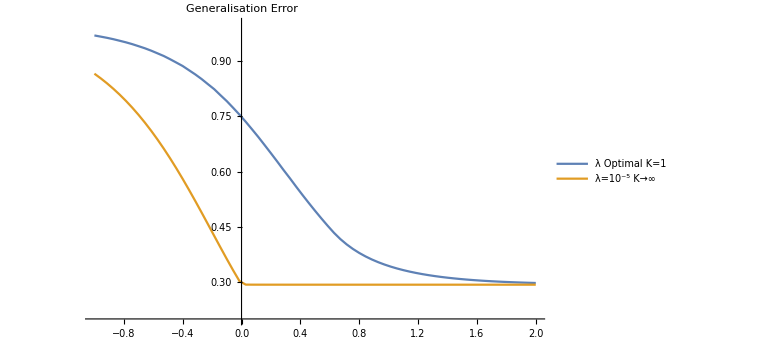
-Graphics-Log10(P/N)

```mathematica
genPlot["pts"->{ptsOpt,ptsBig},"plotRange"->{{-1,2},{0.2,1.0}},"xaxisLabel"->"Log10(P/N)","yaxisLabel"->"Generalisation \n Error","leg"->{"λ Optimal \n K=1","λ=10^-5 \n K→∞ "},"legPos"->{.82,.8}]
```